## Utils

```mathematica
SetDirectory["C:\\Users\\drezn\\Dropbox\\Mathematica"];
```

```mathematica
toDeg[r_]:=180.*r/π;
toRad[d_]:=π*d/180.;
negl[v_]:=Abs[v]<10^-9;
magn2[v_]:=v.v;
magn[v_]:=Sqrt[magn2[v]];
flipY[{x_,y_}]:={x,-y};
flipX[{x_,y_}]:={-x,y};
perp[{x_,y_}]:={-y,x};
perpNeg[{x_,y_}]:={y,-x};
refl[v_,n_]:=2(v.n)n/magn2[n]-v;
norm[v_]:=v/magn[v];
clamp[v_,max_:100]:=If[v>max,max,If[v<-max,-max,v]];
ray[p0_,phat_,d_]:=p0+phat*d;
Clear@rot;
rot[p_,st_,ct_]:=Module[{m},
m={{ct,-st},{st,ct}};
m.p];
rot[p_,t_]:=rot[p,Sin@t,Cos@t];
getEquilateral[th_]:=Module[{s=Sin[2π/3.],c=Cos[2π/3.]},
NestList[rot[#,s,c]&,rot[{1.,0.},Sin@th,Cos@th],2]];
(*x0+nx*t=0= >t=-x0/nx;*)
interY[p0_,phat_]:=Module[{t},
t=-p0[[1]]/phat[[1]];
ray[p0,phat,t]];
(*y0+ny*t=0= >t=-y0/ny;*)
interX[p0_,phat_]:=Module[{t},
t=-p0[[2]]/phat[[2]];
ray[p0,phat,t]];
```

-s (dl.dl)+(p-l1)dl==0⇒ s=(p-l1).dl/dl^2

```mathematica
closestPerp[p_,l1_,l2_]:=Module[{dl=l2-l1,s},
s=((p-l1).dl)/(dl.dl);
ray[l1,dl,s]];
```

```mathematica
Clear@quadRoots;
quadRoots[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
If[det<0,Print["quadRoots fail: {a,b,c}="<>ToString@{a,b,c}];False,
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
Clear@interRays;
interRays[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose[{n1,n2}];(*{{nx1,-nx2},{ny1,-ny2}};*)
If[negl[Det[m]],p1,
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]]
];
interRaysIllConditioned[n1_,n2_]:=negl@Det@Transpose@{n1,n2};
interRaysUnprot[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose@{n1,n2};(*{{nx1,-nx2},{ny1,-ny2}};*)
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]
];
```

```mathematica
Second[l_]:=l[[2]];
Third[l_]:=l[[3]];
```

#### Triangles

```mathematica
cosHalfAngle[cosAngle_]:=Sqrt[(1.+cosAngle)/2];(* careful: plus or minus *)
sinHalfAngle[cosAngle_]:=Sqrt[(1.-cosAngle)/2];
tanHalfAngle[sinAngle_,cosAngle_]:=sinAngle/(1+cosAngle);
(* careful: plus or minus *)
cosDoubleAngle[cosAngle_]:=2*cosAngle*cosAngle-1.; (* cA^2-sA^2 = 2 cA^2-1 *)
sinDoubleAngle[sinAngle_]:=2*sinAngle*Sqrt[1.-sinAngle^2];(* 2 sA cA *)
(* gives cos(A) *)
lawOfCosines[a_,b_,c_]:=(b^2+c^2-a^2)/(2.b c);
getSin[theCos_]:=Sqrt[1.-theCos^2];
sinCosTripleAngle[s_,c_,s2_,c2_]:=Module[{s3,c3},
c3=c2 c-s2 s;
s3=s2 c+s c2;
{s3,c3}];
getSinCosApB[sa_,sb_,ca_,cb_]:={sa cb + sb ca ,ca cb - sa sb};
getSinCosAmB[sa_,sb_,ca_,cb_]:= {sa cb - sb ca,ca cb + sa sb};
getSinApmB[sa_,sb_,ca_,cb_]:= {sa cb + sb ca,sa cb - sb ca};
```

```mathematica
cosDiffAngle[sa_,ca_,sb_,cb_]:=ca cb+sa sb;
cosSumAngle[sa_,ca_,sb_,cb_]:=ca cb-sa sb;
(* compute sin^2(A/2), by passing cosA *)
sin2HalfAngle[cosAngle_]:=(1-cosAngle)/2;(* sinHalfAngle[cos]^2 *)
cos2HalfAngle[cosAngle_]:=(1+cosAngle)/2;(* cosHalfAngle[cos]^2 *)
```

```mathematica
Clear@cosThird;
cosThird[cos_]:=Chop@N@Re[Module[{sin=Sqrt[1-cos^2]},
((cos+I sin)^(-1/3)+(cos+I sin)^(1/3))/2]];
```

```mathematica
Clear@getTriBisectors;
getTriBisectors[p1_,p2_,p3_]:=Module[{u12,u23,u31},
u12=norm[p2-p1];
u23=norm[p3-p2];
u31=norm[p1-p3];
{
norm[u12-u31],
norm[u23-u12],
norm[u31-u23]
}
];
```

#### Ellipse

```mathematica
ellEqn[a_,x_,y_]:=(x/a)^2+y^2-1;
ellEqnb[a_,b_,x_,y_]:=(x/a)^2+(y/b)^2-1;
ellGrad[a_,x_,y_]:=-{x,y a^2};(* (x/a)^2+y^2==1 *)
ellY[a_,x_]:=Sqrt[1-(x/a)^2];
ellError[a_,b_,{x_,y_}]:=(x/a)^2+(y/b)^2-1;
Clear@eccentricity;eccentricity[a_,b_]:=Sqrt[1-(b/a)^2];
focalDistance[a_,b_]:=Sqrt[a^2-b^2];
getFoci=Compile[{{a,_Real}},Module[{c},If[a<1,c=Sqrt[1-a^2];{{0,c},{0,-c}},c=Sqrt[a^2-1];{{-c,0},{c,0}}]]];
getFocib[a_,b_]:=b*getFoci[a/b];
```

```mathematica
ellRayCoeffs=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqn[a,r[[1]],r[[2]]],Assumptions->a>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
FullSimplify[a^2 CoefficientList[eqn,s],a>0]]
```

{x^2+a^2 (-1+y^2),2 (nx x+a^2 ny y),nx^2+a^2 ny^2}

```mathematica
Clear@ellInterRay;
ellInterRay[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRoots[c2,c1,c0];
If[ListQ[ss],
ray[{x,y},{nx,ny},#]&/@ss,
{{x,y},{x,y}}]
];
```

Used for Proofs

```mathematica
quadRootsUnprot[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)];Clear@ellInterRayUnprot;
ellInterRayUnprot[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
Clear@triSides;triSides[vs_]:=MapThread[(#1-#2)&,{vs,RotateLeft@vs}];
Clear@triLengths;triLengths[vs_]:=magn/@triSides[vs];
triPer[tri_]:=Total[triLengths@tri];
(* a,b,c are side lengths *)
Clear@triAreaHeron;triAreaHeron[{a_,b_,c_}]:=Module[{s},
s=(a+b+c)/2;(* semi perimeter *)
Sqrt[s*(s-a)*(s-b)*(s-c)]];
(* order by oposition to vertices *)
getMedians[t1_,t2_,t3_]:={t2+t3,t1+t3,t1+t2}/2;
getMediansV[vs_]:=.5(vs+RotateLeft@vs);
```

```mathematica
Clear@getCircularity;
getCircularity[locus_]:=Module[{rads,ctr,mean,sd},
(* assume it's zero since points may not be evenly distributed so "mean" won't work and RegionCentroid is too slow *)
ctr={0,0};
rads=magn[#-ctr]&/@locus;
mean=Mean@rads;
sd=StandardDeviation@rads;
{
"n"->Length@locus,
"ctr"->ctr,
"min"->Min@rads,
"max"->Max@rads,
"mean"->mean,
"sd"->sd,
"zscore"->sd/mean
}];
```

## Ellipse Inversion, Isogonal and Isotomic Conjugates

-Graphics-
https://arxiv.org/pdf/1309.6378.pdf

```mathematica
Clear@ellInversion;
ellInversion[a_,p_]:=Module[{q,w,p2},
q=ellInterRayUnprot[a,{0,0},p][[2]];
w=q.q;
p2=p.p;
{p*w/p2,q}]
```

```mathematica
ellInversion[1.5,{.5,.5}]
```

{{1.38462,1.38462},{0.83205,0.83205}}

```mathematica
Manipulate[
DynamicModule[{a=1.5,ell,pinv,q,fs,gr},
{ell,fs}={plotEll[a],getFoci[a]};
Dynamic[{pinv,q}=ellInversion[a,p];
gr=Graphics[{PointSize@Large,Point@fs,Red,Point@pinv,Dashed,Line[{p,pinv}],Blue,Point@q}];
Show[{ell,gr},Frame->True,PlotRange->{{-2a,2a},{-2,2}},
PlotLabel->(Style["Inversion with Respect to Ellipse",{Black,Medium}])]]],
{{p,{.5,.5}},Locator},SaveDefinitions->True]
```

```mathematica
(*CloudDeploy[%,"inversion with respect to ellipse",Permissions->"Public"]*)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
Clear@isogonalConjugate;
isogonalConjugate[p_,tri_,bisectors_]:=Module[{refla,reflb,inter},
refla=refl[p-First@tri,First@bisectors];
reflb=refl[p-Second@tri,Second@bisectors];
inter=interRays[First@tri,refla,Second@tri,reflb];
inter];
```

```mathematica
(* could use cevianTriangle, but needs conversion from cartesian to trilinear *)
```

```mathematica
Clear@txtSubscript;
txtSubscript[txt_,subscr_,style_,where_,offset_:{0,0}]:=Text[Style[Subscript[txt,subscr],style],where,offset];
```

```mathematica
Clear@ellLabel;
Options@ellLabel={inward->False};
ellLabel[a_,p_,lgt_,OptionsPattern[]]:=p+If[OptionValue@inward,lgt,-lgt]*norm@ellGrad[a,Sequence@@p];
Clear@ellLabelTxt;
Options@ellLabelTxt={inward->False};
ellLabelTxt[a_,p_,txt_,lgt_,opts:OptionsPattern[]]:=Text[txt,ellLabel[a,p,lgt,{opts}]];
```

```mathematica
Clear@labelPoints;labelPoints[pts_,prefix_,style_,offset_:{0,0}]:=MapThread[txtSubscript[prefix,#1,style,#2,offset]&,{Range@Length@pts,pts}];
```

```mathematica
Clear@ellLabelPoints;ellLabelPoints[a_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts}];
```

```mathematica
Clear@isotomicConjugate;
Options@isotomicConjugate={drGr->False,"drLines"->False,drLabels->False,drLogQprime->False};
isotomicConjugate[p_,tri_,OptionsPattern[]]:=Module[{inters,meds,isos,isoConj,gr,grLines,grLabels,txtD=-1.25},
inters=MapThread[interRays[#1,p-#1,#2,#3-#2]&,{tri,RotateLeft@tri,RotateRight@tri}];
meds=getMedians@@tri;
isos=MapThread[(2#1-#2)&,{meds,inters}];
isoConj=Module[{n1,n2,n3},
n1=isos[[1]]-tri[[1]];
n2=isos[[2]]-tri[[2]];
n3=isos[[3]]-tri[[3]];
Which[
!interRaysIllConditioned[n1,n2],interRaysUnprot[tri[[1]],n1,tri[[2]],n2],
!interRaysIllConditioned[n1,n3],interRaysUnprot[tri[[1]],n1,tri[[3]],n3],
True,interRaysUnprot[tri[[2]],n2,tri[[3]],n3]
]];
gr=If[OptionValue@drGr,{
{FaceForm@None,PointSize@Large,
{Blue,Point@p,Dashed,Text[Style["Q",16],p,{txtD,txtD}]},
{EdgeForm@Black,Polygon@tri,Point@tri,labelPoints[tri,"P",16,{-2,0}]},
{Red,Point@meds},
{Blue,Point@inters},
{Darker@Green,Point@isos,Point@isoConj,Text[Style["Q'",16],isoConj,{txtD,txtD}]},
If[OptionValue@drLogQprime,Module[{isoConjLog},isoConjLog=isoConj@Log[1+norm@isoConj];
{Darker@Green,Point@isoConjLog,Text[Style["log[Q']",16],isoConjLog,{txtD,txtD}]}],{}]}
},{}];

grLines=If[OptionValue@"drLines",{Dashed,
{Blue,MapThread[Line[{#1,#2}]&,{tri,inters}]},
{Darker@Green,MapThread[Line[{#1,#2}]&,{tri,isos}]}},{}];
grLabels=If[OptionValue@drLabels,{
{Red,labelPoints[meds,"m",16,{txtD,0}]},
{Blue,labelPoints[inters,"i",16,{txtD,0}]},
{Darker@Green,labelPoints[isos,"iso",16,{txtD,0}]}},{}];
{isoConj,Graphics/@{gr,grLines,grLabels}}];
```

```mathematica
Manipulate[
DynamicModule[{tri,actData,isoGr,actGr},
tri={{0,0},p2,p3};
isoGr=isotomicConjugate[p0,tri,drGr->True,"drLines"->drLines0,drLabels->drLabels0,drLogQprime->drLogQprime0][[2]];
actGr=If[drACT,
actData=getAnticomplData[tri,RotateLeft@triLengths@tri];
Graphics@{FaceForm@None,EdgeForm@{Blue,Dashed},Polygon@actData["tri"],Darker@Green,Circle[actData["inc"],actData["incR"]],PointSize@Medium,Point@actData["tps"]},
{}];
Show[{isoGr,actGr},
Frame->True,PlotRange->{{-5,5},{-5,5}},PlotLabel->Style["Isotomic Conjugate: Move Q or P_3",{Black,Medium}]]],
{{p0,{.75,.5}},Locator},
{{p2,{1,0}},Locator},
{{p3,{2,2}},Locator},
{{drLines0,False,"isotomic lines"},{True,False}},
{{drLabels0,False,"label points"},{True,False}},
{{drLogQprime0,False,"log Q'"},{True,False}},
{{drACT,False,"anticompl"},{True,False}}]
```

```mathematica
(*CloudDeploy[%,"isotomic conjugate",Permissions->"Public"]*)
```

```mathematica
Manipulate[
DynamicModule[{p1={0,0},p2={1,0},gr,tri,bis,isoConj,p0star,inc,bar,lgt=.2,lgtLine=3},
tri={p1,p2,p3};
inc=getIncenter[tri];
bis=getTriBisectors@@tri;
p0star=isogonalConjugate[p0,tri,bis];
isoConj=isotomicConjugate[p0,tri][[1]];
gr=Graphics[{PointSize@Large,FaceForm@None,Arrowheads@Medium,
EdgeForm@{Thick,Black},Blue,Point@tri,Polygon@tri,Red,Point@p0star,Darker@Green,Point@isoConj,
{Blue,MapThread[Arrow@{#1,#1+lgt*#2}&,{tri,bis}]},
If[drLines,
{Gray,Line@{#,ray[#,norm[p0-#],lgtLine]}&/@tri,Red,Line@{#,ray[#,norm[p0star-#],lgtLine]}&/@tri},{}]}];
Show[gr,PlotRange->{{-.25,1.5},{-.25,1}},Frame->True,
PlotLabel->(Style["Isogonal and Isotomic Conjugates",{Medium,Black}])]],
{{p3,{1.25,.75}},Locator},
{{p0,{.75,.1}},Locator},
{{drLines,False,"isogonal lines"},{True,False}},SaveDefinitions->True]
```

```mathematica
(*CloudDeploy[%,"isogonal conjugate",Permissions->"Public"]*)
```

## Cyclic Quadrilaterals

```mathematica
Clear@orderVertices;
orderVertices[vs_,ctr_]:=Module[{vs0,atans},
vs0=(#-ctr)&/@vs;
atans=ArcTan@@@vs0;
vs[[Ordering[atans]]]];
```

```mathematica
Pick[{a,b,c},{True,False,True}]
```

{a,c}

```mathematica
(* assume ordered *)
Clear@getMaltitudes;getMaltitudes[vs_]:=Module[{ls,vsNonDegen,meds,feet,lines},
ls=MapThread[magn2[#1-#2]&,{vs,RotateLeft@vs}];
vsNonDegen=Pick[vs,Not/@(negl/@ls)];
meds=MapThread[.5(#1+#2)&,{vsNonDegen,RotateLeft@vsNonDegen}];
feet=MapThread[closestPerp[#1,#2,#3]&,{meds,RotateLeft[vsNonDegen,2],RotateLeft[vsNonDegen,3]}];
lines=MapThread[{#1,#2}&,{meds,feet}];
<|"meds"->meds,"feet"->feet,"lines"->lines|>];
```

```mathematica
Manipulate[DynamicModule[{quad,gr,malts},
quad={p1,p2,p3,p4};
malts=getMaltitudes[quad];
gr=Graphics[{FaceForm@None,
{EdgeForm@Blue,Polygon@quad},
{Red,Dashed,Line/@malts["lines"]},
{PointSize@Large,Red,Point@malts["meds"]},
{PointSize@Large,Blue,Point@malts["feet"]}}];
Show[{gr},PlotRange->{{-1,1},{-1,1}}]],
{{p1,{-.5,-.5}},Locator},
{{p2,{.5,-.5}},Locator},
{{p3,{.5,.5}},Locator},
{{p4,{-.5,.5}},Locator}]
```

## Ellipse Invariants

#### Constant Perimeter (Darboux, 1917)

#### -Graphics- Jean-Gaston Darboux (1842-1917)

```mathematica
deltaA[a_]:=Sqrt[a^4-a^2 +1];
```

```mathematica
Clear[darbouxP];
darbouxP[a_,b_:1]:=Module[{a2,b2,delta,per},
a2=a^2;
b2=b^2;
delta=Sqrt[a2^2-a2 b2+b2^2];
per=2Sqrt[2delta-a2-b2](a2+b2+delta)/(a2-b2);
per
];
```

#### Exit angle at x_1 which creates triangular orbit (Garcia, 2019)

-Graphics-

```mathematica
Clear@cosAlpha;cosAlpha[a_,x_]:=Module[{x2,a2,a4,c2,denom},
x2=x^2;
a2=a^2;
a4=a2^2;
c2=a2-1;
denom=c2 Sqrt[a4-c2 x2];
a2 Sqrt[-a2-1+2Sqrt[a4-c2]]/denom];
```

```mathematica
cosAlpha[a,x]//TeXForm
```

\frac{a^2 \sqrt{-a^2+2 \sqrt{a^4-a^2+1}-1}}{\left(a^2-1\right) \sqrt{a^4-\left(a^2-1\right) x^2}}

#### Can I find an expression for the next orbit point P_2 in terms of “a” and x_1

```mathematica
Clear@getP2;getP2[a_,x1_]:=Module[{y,p1,norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
y=-ellY[a,x1];
p1={x1,y};
ca=cosAlpha[a,x1]/.{Sqrt[1-a^2+a^4]->d}/.{-1-a^2+2 d->d2};(* to simplify *)
sa=Sqrt[1-ca^2];
norm=ellGrad[a,x1,y];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

## Triangular Orbits

```mathematica
Clear@getReflData;getReflData [a_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRay[a,p0,nRot][[2]];
interNorm=norm[ellGrad[a,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRay[a,inter,interRefl][[2]];
nextInterNorm=norm[ellGrad[a,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Clear@getOrbitData;
Options@getOrbitData={posY->False};getOrbitData[a_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg},
y=-ellY[a,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGrad[a,x,y]];
ca=cosAlpha[a,x];
sa=Sqrt[1-ca^2];
pos=getReflData[a,o1,n1,sa,ca];
neg=getReflData[a,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->{o1,"inter"/.pos,"nextInter"/.pos},
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
getOrbitData[2.,1.,posY->False]//ColumnForm
```

ca→0.549885
sa→0.835241
halfAlpha→{-0.699945,0.714197}
nRot→{-0.954984,0.296658}
interRefl→{0.999046,0.0436602}
orbit→{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}}
normals→{{-0.27735,0.960769},{0.991722,-0.128403},{-0.898933,-0.438085}}
nRotNeg→{0.649963,0.759966}
interReflNeg→{-0.999046,-0.0436602}
orbitNeg→{{1.,-0.866025},{1.94314,0.236743},{-1.99582,0.0646022}}
normalsNeg→{{-0.27735,0.960769},{-0.898933,-0.438085},{0.991722,-0.128403}}

```mathematica
Clear@orbitDataT;
orbitDataT[a_,t_]:=Module[{ellP},
ellP=N@{a  Cos@t,Sin@t};
getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)]
];
```

```mathematica
Clear@orbitNormals;
orbitNormals[a_,t_]:=Module[{ellP,orbitData},
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit"/.orbitData,"normals"/.orbitData}
];
```

```mathematica
getTriCosines[tri_]:=Module[{u12,u23,u31},
u12=norm[tri[[2]]-tri[[1]]];
u23=norm[tri[[3]]-tri[[2]]];
u31=norm[tri[[1]]-tri[[3]]];
{
-u12.u31,
-u23.u12,
-u31.u23
}];
```

```mathematica
getOrbitCosines[a_,t_]:=Module[{orbit,normals},
{orbit,normals}=orbitNormals[a,t];
getTriCosines[orbit]];
```

```mathematica
Clear@getTriCausticParams;
getTriCausticParams[a_]:=Module[{px,qy,delta},
delta=Sqrt[a^4-a^2+1];
px=a^3/(delta+1);
qy=1/(a^2+delta);
{px,qy}];
```

## Trilinears

Trilinears x : y : z convert via triangle vertices A, B, C  and sides a, b, c :

```mathematica
Clear@trilinearToCartesian;
trilinearToCartesian[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
(a x A+b y B+c z C)/denom];
```

```mathematica
rotateSym[fabc_]:={fabc,fabc/.{a->b,b->c,c->a},fabc/.{a->c,b->a,c->b}}
```

```mathematica
(* trilinears: a:b:c *)
getIncenterTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,{1,1,1}];
getCircumcenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},{a(b2+c2-a2),b(c2+a2-b2),c(a2+b2-c2)}]];
getOrthocenterTrilin[orbit_,sides_]:=Module[{cs},
cs=getTriCosines[orbit];
trilinearToCartesian[orbit,sides,1/cs]
];
getCentroidTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c,c a,a b}];
getFeuerbachTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{b c(b+c-a)(b-c)^2,
c a(c+a-b)(c-a)^2,
a b(a+b-c)(a-b)^2}];
getNinepointCenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},
{b c(a2(b2+c2)-(b2-c2)^2),
c a(b2(c2+a2)-(c2-a2)^2),
a b(c2(a2+b2)-(a2-b2)^2)}]];
```

```mathematica
getX142Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{b+c-(b-c)^2/a,
c+a-(c-a)^2/b,
a+b-(a-b)^2/c
}];
```

```mathematica
(* X(356) *)
getFirstMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,
{c3[[1]]+2c3[[2]] c3[[3]],
c3[[2]]+2c3[[3]] c3[[1]],
c3[[3]]+2c3[[1]] c3[[2]]}]
];
(* X(357) *)
getSecondMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,1/c3]
];
(* X(358) *)
getThirdMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,c3]
];
getSimmedianTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,sides];
getMittenTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-a,c+a-b,a+b-c}];
getGergonneTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b*c/(b+c-a),c*a/(c+a-b),a*b/(a+b-c)}];
getNagelTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c}, {(b+c-a)/a,(c+a-b)/b,(a+b-c)/c}];
getSpiekerTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c(b+c),c a(c+a),a b (a+b)}];
```

```mathematica
Clear@getX144Trilin;
getX144Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,tanAov2,tanBov2,tanCov2},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
tanAov2=tanHalfAngle[sinA,cosA];
tanBov2=tanHalfAngle[sinB,cosB];tanCov2=tanHalfAngle[sinC,cosC];
(* (csc A)(tan B/2+tan C/2-tan A/2) *)
trilinearToCartesian[orbit,{a,b,c},{
(tanBov2+tanCov2-tanAov2)/sinA,
(tanCov2+tanAov2-tanBov2)/sinB,
(tanAov2+tanBov2-tanCov2)/sinC}]];
```

```mathematica
Module[{o,s},
o=orbitNormals[1.5,1.1][[1]];
s=RotateLeft@triLengths[o];
getOrthocenterTrilin[o,s]]
```

{0.696532,1.04352}

```mathematica
Module[{o,n,s,cirs,incs},
{o,n}=orbitNormals[1.5,1.1];
s=RotateLeft@triLengths[o];
cirs={getCircumcenterTrilin[o,s],getCircumcenter@@o};
incs={getIncenterTrilin[o,s],getIncenter[o[[1]],n[[1]],o[[2]],n[[2]]]};
{cirs,incs}//MatrixForm]
```

({-0.0701496,-0.336575} | getCircumcenter[{0.680394,0.891207},{1.3669,-0.41182},{-1.49106,-0.109019}]
{0.449317,0.210191} | getIncenter[{0.680394,0.891207},{-0.321319,-0.946971},{1.3669,-0.41182},{-0.827741,0.561111}])

#### Generate Billiard as Locus

```mathematica
getX100Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b-c,c-a,a-b}];
(*YFF PARABOLIC POINT"*)
getX190Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c/(b-c),c a/(c-a),a b/(a-b)}];
getX88Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-2a,c+a-2b,a+b-2c}];
(* isogonal conjugate of X88, therefore all are inverted *)
getX44Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-2a,c+a-2b,a+b-2c}];
getX693Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{(b-c)/a^2,(c-a)/b^2,(a-b)/c^2}];
```

#### Barycentrics (does not appear to work!)

-Graphics-

```mathematica
barycentricToCartesian[orbit_,lambdas0_]:=Module[{x,y,area,lambdas},
(*area=Area[Polygon@orbit];*)
lambdas=lambdas0/Total@lambdas0;
x=Total@MapThread[(#1*#2)&,{First/@orbit,lambdas}];
y=Total@MapThread[(#1*#2)&,{Second/@orbit,lambdas}];
{x,y}];
```

```mathematica
Clear@X10405;X10405[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
1/{3a^2-2a b-2a c-(b-c)^2,
3b^2-2b c-2b a-(c-a)^2,
3c^2-2c a-2c b-(a-b)^2}];
```

```mathematica
(* perpector of anticomplementary on extouch: http://mathworld.wolfram.com/Perspector.html  *)
```

```mathematica
X144b[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
{1/(a-b-c)+1/(a-b+c)+1/(a+b-c),
1/(b-c-a)+1/(b-c+a)+1/(b+c-a),
1/(c-a-b)+1/(c-a+b)+1/(c+a-b)}];
```

```mathematica
Module[{o,s},
o=orbitNormals[1.5,.1][[1]];
s=RotateLeft@triLengths@o;
{getX144Trilin[o,s],X144b[o,s]}
]
```

{{0.59009,0.346298},{0.59009,0.346298}}

## Triangles form Trilinear Matrices

```mathematica
trilinearMatrixToCartesian[orbit_,sides_,tryM_]:=trilinearToCartesian[orbit,sides,#]&/@tryM;
```

to do : anticomplementary, external tangents triangle.

#### orthic:-Graphics-

#### excentral:-Graphics-

```mathematica
Clear@excentralTriangle;excentralTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,1,1},
{1,-1,1},
{1,1,-1}}];
```

-Graphics-

```mathematica
Clear@medialTriangle;
medialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,a*c,a*b},{b*c,0,a*b},{b*c,a*c,0}}];
```

```mathematica
Module[{tri={{0,0},{1,0},{1,1}}},
medialTriangle[tri,RotateLeft@triLengths@tri]]
```

{{1,1/2},{1/2,1/2},{1/2,0}}

```mathematica
Clear@orthicTriangle;
orthicTriangle[orbit_,sides_]:=Module[{secA,secB,secC},
{secA,secB,secC}=1./getTriCosines[orbit];trilinearMatrixToCartesian[orbit,sides,{{0,secB,secC},{secA,0,secC},{secA,secB,0}}]];
```

```mathematica
(* http://mathworld.wolfram.com/TangentialTriangle.html *)
tangentialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-a,b,c},{a,-b,c},{a,b,-c}}];
anticomplementaryTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{1/{-a,b,c},1/{a,-b,c},1/{a,b,-c}}];
externaltangentsTriangle[orbit_,sides_]:=Module[{x,y,z},
{x,y,z}=getTriCosines[orbit];
trilinearMatrixToCartesian[orbit,sides,
{{-(x+1),x+z,x+y},
{y+z,-(y+1),y+x},
{z+y,z+x,-(z+1)}
}]];
```

-Graphics-

```mathematica
hexylTriangle[orbit_,{a_,b_,c_}]:=Module[{x,y,z,diag},
{x,y,z}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
diag=x+y+z+1;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{diag,x+y-z-1,x-y+z-1},
{x+y-z-1,diag,-x+y+z-1},
{x-y+z-1,-x+y+z-1,diag}}]];
```

```mathematica
outerNapoleonTriangle[orbit_,{a_,b_,c_}]:=Module[{
cosA,cosB,cosC,sinA,sinB,sinC,
cPi6,sPi6,
sApPi6,sBpPi6,sCpPi6,sAmPi6,sBmPi6,sCmPi6},
cPi6=Cos[π/6.];
sPi6=Sin[π/6.];
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{sApPi6,sAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sBpPi6,sBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sCpPi6,sCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,2sCpPi6,2sBpPi6},
{2sCpPi6,-1,2sApPi6},
{2sBpPi6,2sApPi6,-1}}]];
```

```mathematica
firstMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3},
cs={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
cs3=cosThird/@cs;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2cs3[[3]],2cs3[[2]]},
{2cs3[[3]],1,2cs3[[1]]},
{2cs3[[2]],2cs3[[1]],1}}]];
```

```mathematica
cevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{0,t2,t3},{t1,0,t3},{t1,t2,0}}];antiCevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-t1,t2,t3},{t1,-t2,t3},{t1,t2,-t3}}];
```

-Graphics-

```mathematica
intouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a c)/(a-b+c),(a b)/(a+b-c)},
{(b c)/(-a+b+c),0,(a b)/(a+b-c)},
{(b c)/(-a+b+c),(a c)/(a-b+c),0}}];
```

-Graphics-

```mathematica
extouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a-b+c)/b,(a+b-c)/c},
{(-a+b+c)/a,0,(a+b-c)/c},
{(-a+b+c)/a,(a-b+c)/b,0}}];
```

```mathematica
sinHalfAngle[theCos]^2
```

1/2 (1.-theCos)

```mathematica
cosHalfAngle[theCos]^2
```

1/2 (1.+theCos)

-Graphics-

```mathematica
Clear@feuerbachTriangle;
feuerbachTriangle[orbit_,{a_,b_,c_}]:=Module[{
sinA,sinB,sinC,
cosA,cosB,cosC,
cosBmC,cosCmA,cosAmB,
c2haAmB,c2haBmC,c2haCmA,
m},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBmC=cosDiffAngle[sinB,cosB,sinC,cosC];
cosCmA=cosDiffAngle[sinC,cosC,sinA,cosA];
cosAmB=cosDiffAngle[sinA,cosA,sinB,cosB];
c2haAmB=cos2HalfAngle[cosAmB];
c2haBmC=cos2HalfAngle[cosBmC];
c2haCmA=cos2HalfAngle[cosCmA];
m={
{-sin2HalfAngle[cosBmC],c2haCmA,c2haAmB},
{c2haBmC,-sin2HalfAngle[cosCmA],c2haAmB},
{c2haBmC,c2haCmA,-sin2HalfAngle[cosAmB]}
};trilinearMatrixToCartesian[orbit,{a,b,c},m]];
```

```mathematica
Module[{o,s},
o=orbitNormals[1.5,.1][[1]];
s=RotateLeft@triLengths@o;
feuerbachTriangle[o,s]]
```

{{-1.04832,-0.369712},{-0.112968,0.352287},{0.256211,-0.740368}}

#### The first point in the extouch triangle flows on caustic at the exact same parametric than P1

```mathematica
Manipulate[Module[{o,ett,ell,a=1.5,gr,ca,cb},
o=orbitNormals[a,t][[1]];
{ca,cb}=getTriCausticParams[a];
ett=extouchTriangle[o,RotateLeft@triLengths@o];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@{Blue,Thick},Polygon@o,Red,Point@First@o,Blue,Circle[First@o,.05]},
{EdgeForm@Darker@Green,Polygon@ett},
{Darker@Green,Circle[ett[[1]],.05]},
{Red,Point[{-ca Cos[t],-cb Sin[t]}]}}];
Show[{plotEll[a],plotEllb[ca,cb,Brown],gr},AspectRatio->Automatic,Frame->True]],{t,0,2π,π/360.}]
```

#### Anticomplementary triangle seems like the more stable, more useful to produce higher order points.

```mathematica
Module[{cc,vs,sides,cir,cirRad,tt,ac,et,ortTril,ortCev,clrs,ort,ortAntiCev,hexyl},
Manipulate[
vs={{-1,0},{1,0},p1}; (*N@{{0,0},{1,-.6},{.7,.5}};*)
sides=RotateLeft@triLengths@vs;
cir=getCircumcenterTrilin[vs,sides];
cirRad=magn[vs[[1]]-cir];
tt=tangentialTriangle[vs,sides];
ac=anticomplementaryTriangle[vs,sides];
et=externaltangentsTriangle[vs,sides];
hexyl=hexylTriangle[vs,sides];
ortTril=1/getTriCosines[vs];
ort=trilinearToCartesian[vs,sides,ortTril];
ortCev=cevianTriangle[vs,sides,ortTril];
ortAntiCev=antiCevianTriangle[vs,sides,ortTril];
clrs={Black,Red,Green,Blue,Purple,Cyan,Pink};
Legended[Graphics[{PointSize@Medium,Black,FaceForm@None,
MapThread[{EdgeForm@#1,#1,Polygon@#2,Point@#2}&,{clrs,{vs,tt,ac,et,ortCev,ortAntiCev,hexyl}}],
{Circle[cir,cirRad],Point@cir},
{Orange,Point@ort}},ImageSize->Medium,Frame->True,PlotRange->{{-5,5},{-5,5}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"reference","tangential","anticomplementary","external tangents","ortho cevian = orthic","ortho anticevian","hexyl"}]],
{{p1,{0,2}},Locator},SaveDefinitions->True]]
```

-Graphics-

```mathematica
getInradius[{a_,b_,c_}]:=Module[{num1,num2,num3,denom},
num1=(b+c-a);
num2=(c+a-b);
num3=(a+b-c);
denom=a+b+c;
Sqrt[num1*num2*num3/denom]/2];
```

-Graphics-

```mathematica
getCircumradius[{a_,b_,c_}]:=Module[{s,num,denom1,denom2,denom3},
s=(a+b+c)/2;
num=a*b*c;
denom1=(a+b-s);
denom2=(a+c-s);
denom3=(b+c-s);
num/(4*Sqrt[s*denom1*denom2*denom3])];
```

```mathematica
getNinepointCircleRadius[sides_]:=getCircumradius[sides]/2;
```

```mathematica
getTriCosines[tri_]:=Module[{u12,u23,u31},
u12=norm[tri[[2]]-tri[[1]]];
u23=norm[tri[[3]]-tri[[2]]];
u31=norm[tri[[1]]-tri[[3]]];
{
-u12.u31,
-u23.u12,
-u31.u23
}];
```

```mathematica
getTriData[tri_]:=Module[{sides,perimeter,inc,inradius,circumradius,cosines,bisectors},
sides=RotateLeft@triLengths@tri;
perimeter=Total@sides;
inradius=getInradius[sides];
circumradius=getCircumradius[sides];
cosines=getTriCosines[tri];
bisectors=getTriBisectors@@tri;
{"sides"->sides,
"perimeter"->perimeter,
"inradius"->inradius,
"circumradius"->circumradius,
"rOvR"->inradius/circumradius,
"cosines"->cosines,
"bisectors"->bisectors}];
```

```mathematica
getSubtriData[tri_]:=Module[{sides,inc,tps,incR,npc,npcR},
sides=RotateLeft[triLengths@tri];
inc=getIncenterTrilin[tri,sides];
(* the intouchpoints of this guy is on the billiard, needs to draw them *)
tps=intouchTriangle[tri,sides];
incR=getInradius[sides];
npc=getNinepointCenterTrilin[tri,sides];
npcR=getNinepointCircleRadius[sides];
<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];
```

```mathematica
Clear@getAnticomplData;
getAnticomplData[orbit_,sides_]:=
getSubtriData@anticomplementaryTriangle[orbit,sides];
```

```mathematica
Clear@getMedialData;
getMedialData[orbit_,sides_]:=
getSubtriData@medialTriangle[orbit,sides];
```

```mathematica
getTriDoubleCosineSum[tri_]:=Total[cosDoubleAngle/@getTriCosines@tri];
```

## Major Triangular Centers (Notables)

#### Linha de Euler: bari, ortho, circum, 9-pc all lie on a line (but not incenter)

-Graphics-

```mathematica
getAltBases[p1_,p2_,p3_]:=Module[{sides},
sides={{p2,p3},{p3,p1},{p1,p2}};
MapThread[closestPerp[#1,#2[[1]],#2[[2]]]&,{{p1,p2,p3},sides}]];
```

```mathematica
getIncenter[p1_,n1_,p2_,n2_]:=interRays[p1,n1,p2,n2];
Clear@getBaricenter;getBaricenter[p1_,p2_,p3_]:=Module[{medians},(*(p1+p2+p3)/3;*)
medians=getMedians[p1,p2,p3];
interRays[p1,medians[[1]](*23*)-p1,p2,medians[[2]](*31*)-p2]
];
getOrthocenter[p1_,p2_,p3_]:=Module[{altBases},
altBases=getAltBases[p1,p2,p3];
interRays[p1,altBases[[1]]-p1,p2,altBases[[2]]-p2]
];
getCircumcenter[p1_,p2_,p3_]:=Module[{medians,medianPerps},
medians=getMedians[p1,p2,p3];
medianPerps={
medians[[1]]+norm[perp[p2-p3]],
medians[[2]]+norm[perp[p3-p1]],
medians[[3]]+norm[perp[p1-p2]]
};
interRays[medians[[1]](*2+3*),perp[p2-p3],medians[[2]](*3+1*),perp[p1-p3]]
];
```

#### Nine Point Circle: its center is the circumcenter of the medians, and is tangent to incircle (at Feuerbach point) and all 3 excircles

-Graphics--Graphics-

```mathematica
getNinepointcenter[p1_,p2_,p3_]:=Module[{medians},
medians=getMedians[p1,p2,p3];
getCircumcenter@@medians
];
```

```mathematica
Clear@inRadius0;
inRadius0[incenter_,p1_,p2_]:=Module[{ctr,foot},
foot=closestPerp[incenter,p1,p2];
magn[incenter-foot]];
```

```mathematica
circumRadius0[circumcenter_,p1_]:=magn[circumcenter-p1];
```

```mathematica
(* shoot ray from incenter *)
getFeuerbachpoint[npc_,incenter_,inradius_]:=Module[{inter},
ray[incenter,norm[incenter-npc],inradius]
];
```

```mathematica
getExcenters[orbit_,normals_]:=Module[{perps,perpsNeg,exc},
perps=perp/@normals;
perpsNeg=perpNeg/@normals;
exc=MapThread[interRays[#1,#2,#3,#4]&,{orbit,perps,RotateLeft@orbit,RotateLeft@perpsNeg}];
exc];
```

#### Gergonne Point: perspector of ABC and its contact triangle Ta, Tb, Tc

## Get Triangular Center (Notable) Info

```mathematica
Clear@getTouchPts;getTouchPts[orbit_,normals_]:=Module[{inc,tps},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
tps];
```

```mathematica
getAntiComplement[p_,bar_]:=bar-2(p-bar);
```

```mathematica
Clear@getNotables;
getNotables[orbit_,normals_]:=Module[{inc,inradius,cir,circumradius,npc,exc,tps,ort,medians,npcradius,sides,bar,feu,antifeu,x88,perimeter},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
inradius=inRadius0[inc,orbit[[1]],orbit[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
medians=getMedians@@orbit;
cir=getCircumcenter@@orbit;
circumradius=circumRadius0[cir,orbit[[1]]];
npc=getNinepointcenter@@orbit;
npcradius=magn[npc-medians[[1]]];
exc=getExcenters[orbit,normals];
sides=RotateLeft[triLengths@orbit];
feu=getFeuerbachpoint[npc,inc,inradius];
bar=getBaricenter@@orbit;
antifeu=getAntiComplement[feu,bar];(* anticomplement *)
x88=getX88Trilin[orbit,sides];
ort=getOrthocenter@@orbit;
perimeter=Total@sides;
(* we think this is constant for excentral triangle *)
{
"inc"->inc,
"bar"->bar,(* also: getCentroid[orbit,sides] *)
"ort"->ort,
"cir"->cir,
"npc"->npc,
"exc"->exc,
"ex12"->exc[[1]],
"ex23"->exc[[2]],
"ex31"->exc[[3]],
"feu"->feu,
"antifeu"->antifeu,
"x88"->x88,
(* all thru trilinears, each computing sides unnecessarily *)
"mit"->getMittenTrilin[orbit,sides],
"sym"->getSimmedianTrilin[orbit,sides],
"ger"->getGergonneTrilin[orbit,sides],
"nag"->getNagelTrilin[orbit,sides],
"spi"->getSpiekerTrilin[orbit,sides],
(* not really notables, aux info *)
"incRadius"->inradius,
"tps"-> tps,
"medians"->medians,
"cirRadius"->circumradius,
"npcRadius"->npcradius,
"sides"->sides,
"perimeter"->perimeter,
"area"->triAreaHeron@sides
}];
```

#### Orthic and orthic of orthic (similar to reference triangle?)

```mathematica
Clear@getOrthicData;getOrthicData[orbit_]:=Module[{feet,inc,sides,ort,
intouch,intouchSides,inradius,(* intouchInc = inc *)
intouchOrt,intouchOrtSides,intouchOrtInc,
intouchAnticompl,intouchAnticomplSides,
intouchAnticomplOrt,intouchAnticomplOrtSides,intouchAnticomplOrtInc,
orthic,orthicSides,orthicInc,
orthicAnticompl,orthicAnticomplSides,orthicAnticomplInc
},
(* orthic *)
feet=getAltBases@@orbit;
sides=RotateLeft@triLengths[feet];
inc=getIncenterTrilin[feet,sides];
ort=getOrthocenterTrilin[feet,sides];
(* intouch *)
intouch=intouchTriangle[feet,sides];
intouchSides=RotateLeft[triLengths@intouch];
inradius=magn[intouch[[1]]-inc];
intouchOrt=getAltBases@@intouch;
intouchOrtSides=RotateLeft[triLengths@intouchOrt];
intouchOrtInc=getIncenterTrilin[intouchOrt,intouchOrtSides];
(* anticomplement of intouch *)
intouchAnticompl=anticomplementaryTriangle[intouch,intouchSides];
intouchAnticomplSides=RotateLeft[triLengths@intouchAnticompl];
intouchAnticomplOrt=getAltBases@@intouchAnticompl;
intouchAnticomplOrtSides=RotateLeft[triLengths@intouchAnticomplOrt];
intouchAnticomplOrtInc=getIncenterTrilin[intouchAnticomplOrt,intouchAnticomplOrtSides];
(* orthic *)
orthic=getAltBases@@feet;
orthicSides=RotateLeft@triLengths[orthic];
orthicInc=getIncenterTrilin[orthic,orthicSides];
orthicAnticompl=anticomplementaryTriangle[orthic,orthicSides];
orthicAnticomplSides=RotateLeft@triLengths[orthicAnticompl];
orthicAnticomplInc=getIncenterTrilin[orthicAnticompl,orthicAnticomplSides];
{
(* orthic *)
"feet"->feet,
"sides"->sides,
"inc"->inc,
"ort"->ort,
(* intouch of orthic, we think similar to orbit *)
"intouch"->intouch,
"intouchSides"->intouchSides,
"inradius"->inradius,
(* orthic of intouch *)
"intouchOrt"->intouchOrt,
"intouchOrtSides"->intouchOrtSides,
"intouchOrtInc"->intouchOrtInc,
(* anticomplement of intouch of orthic, upside down orbit? *)
"intouchAnticompl"->intouchAnticompl,
"intouchAnticomplSides"->intouchAnticomplSides,
(*"intouchAnticomplInc"->intouchAnticomplInc,*)
(* orthic of anticomplement of intouch *)
"intouchAnticomplOrt"->intouchAnticompl,
"intouchAnticomplOrtSides"->intouchAnticomplOrtSides,
"intouchAnticomplOrtInc"->intouchAnticomplOrtInc,
(* orthic of orthic *)
"orthic"->orthic,
"orthicSides"->orthicSides,
"orthicInc"->orthicInc,
(* anticomplement of orthic's orthic *)
"orthicAnticompl"->orthicAnticompl;
"orthicAnticomplSides"->orthicAnticomplSides,
"orthicAnticomplInc"->orthicAnticomplInc
}];
```

#### Excenters and Excircles

```mathematica
Clear@showBisectors;showBisectors[vs_]:=Module[{bs},
bs=getTriBisectors@@vs;
Graphics[{FaceForm[None],EdgeForm[Black],Black,PointSize[Medium],
Polygon[vs],
Point[vs],
MapThread[Text[#1,#2,{1.5,0}]&,{{"P_1","P_2","P_3"},vs}],
MapThread[Arrow[{#1,ray[#1,#2,.25]}]&,{vs,bs}]},
ImageSize->Small]
];
```

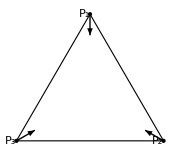

```mathematica
(* show bisectors computed from vertices for equilateral *)
showBisectors[Table[{Sin[a],Cos[a]},{a,0,2π-π/3,2π/3}]]
```

#### Nagel Point

```mathematica
getExtouchPoints[orbit_,exc_]:=MapThread[closestPerp[#1,#2,#3]&,{exc,orbit,RotateLeft[orbit]}];
```

```mathematica
Clear@getExcircleData;
getExcircleData[orbit_,exc_(*12,23,31*),npc_]:=Module[{excFeet,altLengths,tps,radii,feus,nagel,medians,mitten,mittenPedals,
mittenFeet,sides,cosABC,cosSum,cosProd,sideProd,altLengthsProd},
(* side touch points to sides: 12,23,31 *)
tps=getExtouchPoints[orbit,exc];
excFeet=getAltBases@@exc;
altLengths=MapThread[magn[#1-#2]&,{exc,excFeet}];
radii=MapThread[magn[#1-#2]&,{exc,tps}];
feus=MapThread[ray[#1,norm[npc-#1],#2]&,{exc,radii}];
(*nagel=interRays[orbit[[1]],tps[[2]]-orbit[[1]],orbit[[2]],tps[[3]]-orbit[[2]]];*)
(* MapThread[Line[{#1,ray[#1,norm[#2-#1],10]}]&,{exc,RotateRight@medians}]}],{}],*)
medians=getMedians@@orbit;
mitten=interRays[exc[[1]],medians[[3]]-exc[[1]],exc[[2]],medians[[1]]-exc[[2]]];
mittenPedals=MapThread[closestPerp[mitten,#1,#2]&,{orbit,RotateLeft@orbit}];
mittenFeet=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{exc,RotateRight@medians,RotateLeft@exc,RotateRight@exc}];
sides=RotateLeft[triLengths@exc];
cosABC=getTriCosines[exc];
cosSum=Total[cosABC];
cosProd=cosABC[[1]]*cosABC[[2]]*cosABC[[3]];
sideProd=sides[[1]]*sides[[2]]*sides[[3]];
altLengthsProd=altLengths[[1]]*altLengths[[2]]*altLengths[[3]];
{
"sides"->sides,
"perimeter"->Total[sides],
"cosABC"->cosABC,
"excFeet"->excFeet,
"altLengths"->altLengths,
"sumAltLengths"->Total@altLengths,
"prodAltLengths"->altLengthsProd,
"sumInvAltLengths"->Total[(1/#)&/@altLengths],
"cosSum"->cosSum,
"cosProd"->cosProd,
"sideProd"->sideProd,
"tps"->tps,(* extouchpoints*)
"radii"->radii,
"sumRadiiSqr"->Total[#^2&/@radii],
"sumInvRadiiSqr"->Total[(1/#^2)&/@radii],
"sumRadii"->Total@radii,
"sumInvRadii"->Total[(1/#)&/@radii],
"feus"->feus,
"mitten"->mitten,
"mittenPedals"->mittenPedals,
"mittenFeet"-> mittenFeet (* BAD choice: intersecao do segm Vi-MITTEN com o lado oposto do extriangulo *)
}
];
```

## Legacy Colors

```mathematica
ColorData["Legacy","ColorRules"]//Partition[#,6]&//Grid[#,Alignment->Left]&
```

AliceBlue→-Graphics- | AlizarinCrimson→-Graphics- | Antique→-Graphics- | Apricot→-Graphics- | Aquamarine→-Graphics- | AureolineYellow→-Graphics-
Azure→-Graphics- | Banana→-Graphics- | Beige→-Graphics- | Bisque→-Graphics- | Black→-Graphics- | BlanchedAlmond→-Graphics-
Blue→-Graphics- | BlueViolet→-Graphics- | Brick→-Graphics- | Brown→-Graphics- | BrownMadder→-Graphics- | BrownOchre→-Graphics-
Burlywood→-Graphics- | BurntSienna→-Graphics- | BurntUmber→-Graphics- | CadetBlue→-Graphics- | CadmiumLemon→-Graphics- | CadmiumOrange→-Graphics-
CadmiumYellow→-Graphics- | Carrot→-Graphics- | Cerulean→-Graphics- | Chartreuse→-Graphics- | Chocolate→-Graphics- | ChromeOxideGreen→-Graphics-
CinnabarGreen→-Graphics- | Cobalt→-Graphics- | CobaltGreen→-Graphics- | ColdGray→-Graphics- | Coral→-Graphics- | CornflowerBlue→-Graphics-
Cornsilk→-Graphics- | Cyan→-Graphics- | CyanWhite→-Graphics- | DarkGoldenrod→-Graphics- | DarkGreen→-Graphics- | DarkKhaki→-Graphics-
DarkOliveGreen→-Graphics- | DarkOrange→-Graphics- | DarkOrchid→-Graphics- | DarkSeaGreen→-Graphics- | DarkSlateBlue→-Graphics- | DarkSlateGray→-Graphics-
DarkTurquoise→-Graphics- | DarkViolet→-Graphics- | DeepCadmiumRed→-Graphics- | DeepCobaltViolet→-Graphics- | DeepMadderLake→-Graphics- | DeepNaplesYellow→-Graphics-
DeepOchre→-Graphics- | DeepPink→-Graphics- | DeepSkyBlue→-Graphics- | DimGray→-Graphics- | DodgerBlue→-Graphics- | Eggshell→-Graphics-
EmeraldGreen→-Graphics- | EnglishRed→-Graphics- | Firebrick→-Graphics- | Floral→-Graphics- | ForestGreen→-Graphics- | Gainsboro→-Graphics-
GeraniumLake→-Graphics- | Ghost→-Graphics- | Gold→-Graphics- | Goldenrod→-Graphics- | GoldOchre→-Graphics- | Gray→-Graphics-
Green→-Graphics- | GreenishUmber→-Graphics- | GreenYellow→-Graphics- | Honeydew→-Graphics- | HotPink→-Graphics- | IndianRed→-Graphics-
Indigo→-Graphics- | Ivory→-Graphics- | IvoryBlack→-Graphics- | Khaki→-Graphics- | LampBlack→-Graphics- | Lavender→-Graphics-
LavenderBlush→-Graphics- | LawnGreen→-Graphics- | LemonChiffon→-Graphics- | LightBeige→-Graphics- | LightBlue→-Graphics- | LightCadmiumRed→-Graphics-
LightCadmiumYellow→-Graphics- | LightCoral→-Graphics- | LightGoldenrod→-Graphics- | LightGray→-Graphics- | LightPink→-Graphics- | LightSalmon→-Graphics-
LightSeaGreen→-Graphics- | LightSkyBlue→-Graphics- | LightSlateBlue→-Graphics- | LightSlateGray→-Graphics- | LightSteelBlue→-Graphics- | LightViridian→-Graphics-
LightYellow→-Graphics- | LimeGreen→-Graphics- | Linen→-Graphics- | Magenta→-Graphics- | ManganeseBlue→-Graphics- | Maroon→-Graphics-
MarsOrange→-Graphics- | MarsYellow→-Graphics- | MediumAquamarine→-Graphics- | MediumBlue→-Graphics- | MediumOrchid→-Graphics- | MediumPurple→-Graphics-
MediumSeaGreen→-Graphics- | MediumSlateBlue→-Graphics- | MediumSpringGreen→-Graphics- | MediumTurquoise→-Graphics- | MediumVioletRed→-Graphics- | Melon→-Graphics-
MidnightBlue→-Graphics- | Mint→-Graphics- | MintCream→-Graphics- | MistyRose→-Graphics- | Moccasin→-Graphics- | Navajo→-Graphics-
Navy→-Graphics- | NavyBlue→-Graphics- | Oak→-Graphics- | OldLace→-Graphics- | Olive→-Graphics- | OliveDrab→-Graphics-
Orange→-Graphics- | OrangeRed→-Graphics- | Orchid→-Graphics- | PaleGoldenrod→-Graphics- | PaleGreen→-Graphics- | PaleTurquoise→-Graphics-
PaleVioletRed→-Graphics- | PapayaWhip→-Graphics- | Peach→-Graphics- | PeachPuff→-Graphics- | Peacock→-Graphics- | PermanentGreen→-Graphics-
PermanentRedViolet→-Graphics- | Peru→-Graphics- | Pink→-Graphics- | Plum→-Graphics- | PowderBlue→-Graphics- | PrussianBlue→-Graphics-
Purple→-Graphics- | Raspberry→-Graphics- | RawSienna→-Graphics- | RawUmber→-Graphics- | Red→-Graphics- | RoseMadder→-Graphics-
RosyBrown→-Graphics- | RoyalBlue→-Graphics- | SaddleBrown→-Graphics- | Salmon→-Graphics- | SandyBrown→-Graphics- | SapGreen→-Graphics-
SeaGreen→-Graphics- | Seashell→-Graphics- | Sepia→-Graphics- | Sienna→-Graphics- | SkyBlue→-Graphics- | SlateBlue→-Graphics-
SlateGray→-Graphics- | Smoke→-Graphics- | Snow→-Graphics- | SpringGreen→-Graphics- | SteelBlue→-Graphics- | TerreVerte→-Graphics-
Thistle→-Graphics- | Titanium→-Graphics- | Tomato→-Graphics- | Turquoise→-Graphics- | TurquoiseBlue→-Graphics- | Ultramarine→-Graphics-
UltramarineViolet→-Graphics- | VanDykeBrown→-Graphics- | VenetianRed→-Graphics- | Violet→-Graphics- | VioletRed→-Graphics- | WarmGray→-Graphics-
Wheat→-Graphics- | White→-Graphics- | Yellow→-Graphics- | YellowBrown→-Graphics- | YellowGreen→-Graphics- | YellowOchre→-Graphics-

## Drawing Notables & Clrs

```mathematica
ptClrs={
"ell"->Black,
"med"->Red,
"bar"->Purple,
"inc"->Darker@Green,
"ort"->Orange,
"cir"->Lighter@Purple,
"npc"->RGBColor[1.,0.02,0.3],
"exc"->Darker@Green,
"ex12"->Darker@Green,
"ex23"->Darker@Green,
"ex31"->Darker@Green,
"feu"-> RGBColor[0.5,0.5,0.27],
"antifeu"->Orange,
"anticompl"->Blue,
"steiner"->Pink,
"x88"->Darker@Cyan,
"dar"-> ColorData["Legacy","Violet"],
"tab"-> ColorData["Legacy","UltramarineViolet"],
"nag"->Red,
"mit"->Red(*Lighter@Blue*),
"sym"->Purple,
"ger"->Pink,
"spi"->Darker@Cyan,
"nap"->Red,
"hex"->Pink,
(* overrides *)
"red"->Red,
"green"->Green,
"blue"->Blue
};
```

```mathematica
Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
plotEllFill[a_,clrFill_,clr_:("ell"/.ptClrs)]:=Module[{int,ext},
int=ParametricPlot[r{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},{r,0,1},
PlotStyle->clrFill,PerformanceGoal->"Quality"];
ext=plotEll[a,clr];
Show[{int,ext}]];
plotEllb[a_,b_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],N[b]Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
```

```mathematica
drawArrow[p0_,phat_,l_]:=Arrow[{p0,ray[p0,phat,l]}];
```

```mathematica
Clear@drawOrbit;
drawOrbit[orbitData_,lgt_:.25,drawNormals_:True,psize_:16]:=Module[{normals,orbit,halfAlpha},
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
halfAlpha="halfAlpha"/.orbitData;
Graphics[{
PointSize[Large],Arrowheads[Medium],
{Black,Point@orbit},
{FaceForm[GrayLevel[.95]],EdgeForm[{Thick,Black}],Polygon@orbit},
If[drawNormals,
{Black,
MapThread[drawArrow[#1,#2,lgt]&,{orbit,normals}],
Dashed,
drawArrow[orbit[[1]],"nRot"/.orbitData,lgt],
drawArrow[orbit[[1]],"nRotNeg"/.orbitData,lgt],
Text["α",ray[orbit[[1]],halfAlpha ,lgt*.33]]},{}],
MapThread[txtSubscript["P",ToString@#1,psize,ray[#2,-#3,lgt*.33]]&,
{{1,2,3},orbit,normals}]}]
];
```

```mathematica
Clear@drawOneNotable;drawOneNotable[clr_,at_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Point@at,Text[Style[txt,fntSize],at,{dx,dy}]};
circOneNotable[clr_,at_,rad_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Circle[at,rad],Text[Style[txt,fntSize],at,{dx,dy}]};
Clear@drawNotableLines;drawNotableLines[notables_]:=Graphics@{Darker[Gray],Dashed,
(* euler line: cir,bar,npc,ort *)
Line[{"cir","ort"}/.notables],
(* npc to feuerbach: npc,inc,feu *)
Line[{"npc","feu"}/.notables],
(* mittenpunkt to symmedian: mit,inc,sym *)
Line[{"mit","sym"}/.notables],
(* gergonne to mit: ger,bar,mit *)
Line[{"mit","ger"}/.notables],
(* nagel line: nag,bar,spi,inc *)
Line[{"nag","inc"}/.notables]};
Clear@drawNotables;
drawNotables[notables_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
drawNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotables;
circNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotablesSingleClr;
circNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@drawSomeNotables;
drawSomeNotables[notables_,nots_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@nots}];
Clear@drawBasicNotables;
drawBasicNotables[notables_,prefix_:""]:=drawSomeNotables[notables,{"inc","bar","ort","cir","npc","mit","feu","ger"},prefix];
Clear@drawBasicNotablesSingleClr;
drawBasicNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotables;
circBasicNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotablesSingleClr;
circBasicNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
```

Formatting

```mathematica
nfn[v_,n_]:=ToString@NumberForm[v,{n+2,n}];
nf[v_]:=ToString@NumberForm[v,{3,2}];
nf1[v_]:=ToString@NumberForm[v,{3,1}];
nf0[v_]:=ToString@IntegerPart[v];
```

## Draw Orbits: Parametrize by x_1

```mathematica
Clear@drawSim;
Options@drawSim=Join[Options@getOrbitData,{drNotables->True,drLines->False}];
drawSim[a_,x_,opts:OptionsPattern[]]:=Module[{ellPlot,orbitData,orbit,normals,notables,lgt=.5},
ellPlot=plotEll[a];
orbitData=getOrbitData[N[a],N[x], FilterRules[{opts}, Options@getOrbitData]];(* N for speed *)
(* half-angle to display α at bisector *)
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
notables=getNotables[orbit,normals];
Show[{
ellPlot,
drawOrbit[orbitData,lgt],
If[OptionValue@drNotables,drawNotables[notables],{}],
If[OptionValue@drLines,drawNotableLines[notables],{}]
},
ImageSize->Large,
AspectRatio->Automatic,
PlotRange->{{-2,2},{-1.1,1.1}},Frame->True,AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style["a="<>nf@a<>"; x="<>nf@x,20]]];
```

```mathematica
Manipulate[
drawSim[a,clamp[x1,a],drLines->drLines0,posY->(!negY),drNotables->drNotables0],
{{a,1.5,"a/b"},1.01,3,.01,Appearance->"Labeled"},
{{x1,.5,"x_1"},-2,2,.01,Appearance->"Labeled"},
{{negY,False,"y_1<0"},{False,True}},
{{drNotables0,True,"show notables"},{False,True}},
{{drLines0,False,"show lines"},{False,True}},
SaveDefinitions->True]
```

```mathematica
(*CloudDeploy[%,"view notables",Permissions->"Public"]*)
```

## Trilinears: X(1)~X(100)

```mathematica
Clear@getNewCenters;
getNewCenters[orbit_,{a_,b_,c_},singles_:{}]:=Block[{eqns,
cosA,cosB,cosC,sinA,sinB,sinC,
secA,secB,secC,cscA,cscB,cscC,
tanA,tanB,tanC,cotA,cotB,cotC,
cos2A,cos2B,cos2C,sin2A,sin2B,sin2C,
sec2A,sec2B,sec2C,csc2A,csc2B,csc2C,
cos3A,sin3A,cos3B,sin3B,cos3C,sin3C,
sec3A,sec3B,sec3C,csc3A,csc3B,csc3C,
cPi3=Cos[π/3.],sPi3=Sin[π/3.],cPi6=Cos[π/6.],sPi6=Sin[π/6.],
sinApPi3,sinBpPi3,sinCpPi3,sinAmPi3,sinBmPi3,sinCmPi3,
sinApPi6,sinBpPi6,sinCpPi6,sinAmPi6,sinBmPi6,sinCmPi6,
cscApPi3,cscBpPi3,cscCpPi3,cscAmPi3,cscBmPi3,cscCmPi3,
cscApPi6,cscBpPi6,cscCpPi6,cscAmPi6,cscBmPi6,cscCmPi6},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1./{cosA,cosB,cosC};
{cscA,cscB,cscC}=1./{sinA,sinB,sinC};
{tanA,tanB,tanC}={sinA,sinB,sinC}/{cosA,cosB,cosC};
{cotA,cotB,cotC}=1./{tanA,tanB,tanC};
{cos2A,cos2B,cos2C}=cosDoubleAngle/@{cosA,cosB,cosC};
{sec2A,sec2B,sec2C}=1./{cos2A,cos2B,cos2C};
{sin2A,sin2B,sin2C}=getSin/@{cos2A,cos2B,cos2C};
{csc2A,csc2B,csc2C}=1./{sin2A,sin2B,sin2C};
{sin3A,cos3A}=sinCosTripleAngle[sinA,cosA,sin2A,cos2A];
{sin3B,cos3B}=sinCosTripleAngle[sinB,cosB,sin2B,cos2B];
{sin3C,cos3C}=sinCosTripleAngle[sinC,cosC,sin2C,cos2C];
{sec3A,sec3B,sec3C}=1./{cos3A,cos3B,cos3C};
{csc3A,csc3B,csc3C}=1./{sin3A,sin3B,sin3C};
{sinApPi3,sinAmPi3}=getSinApmB[sinA,sPi3,cosA,cPi3];
{sinBpPi3,sinBmPi3}=getSinApmB[sinB,sPi3,cosB,cPi3];
{sinCpPi3,sinCmPi3}=getSinApmB[sinC,sPi3,cosC,cPi3];
{sinApPi6,sinAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sinBpPi6,sinBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sinCpPi6,sinCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
{cscApPi3,cscBpPi3,cscCpPi3}=1./{sinApPi3,sinBpPi3,sinCpPi3};
{cscAmPi3,cscBmPi3,cscCmPi3}=1./{sinAmPi3,sinBmPi3,sinCmPi3};
{cscApPi6,cscBpPi6,cscCpPi6}=1./{sinApPi6,sinBpPi6,sinCpPi6};
{cscAmPi6,cscBmPi6,cscCmPi6}=1./{sinAmPi6,sinBmPi6,sinCmPi6};
eqns=Get["data/x0001_0100.m"];
Chop[{
#[[1]],#[[3]],
trilinearToCartesian[orbit,{a,b,c},N@ReleaseHold[#[[2]]]]}&/@
(* if singles ≠ {}, use the list to only evaluate requested indices *)
If[Length[singles]>0,eqns[[singles]],eqns]]
];
```

```mathematica
List@@@Take[((Second@#)&/@Get["data/x0001_0100.m"]),3]
```

{{{1,1,1}},{{b c,a c,a b}},{{cosA,cosB,cosC}}}

```mathematica
centerEqns=TraditionalForm@First@First@#&/@List@@@((Second@#)&/@Get["data/x0001_0100.m"]);
centerNames=(#[[1]]<>": "<>#[[2]])&/@Quiet@getNewCenters[{{0,0},{1,0},{1,1}},RotateLeft@{1,1,Sqrt[2.]}];
```

```mathematica
Clear@newCenters;newCenters[a_,t_,singles_:{}]:=Module[{orbit,normals,sides},
{orbit,normals}=orbitNormals[a,t];
orbit=Reverse@orbit;
sides=RotateLeft[triLengths[orbit]];
getNewCenters[orbit,sides,singles]
];
```

```mathematica
Clear@newCentersAnticompl;
newCentersAnticompl[a_,t_,singles_:{}]:=Module[{orbit,normals,sides,act,sidesAct},
{orbit,normals}=orbitNormals[a,t];
orbit=Reverse@orbit;
sides=RotateLeft@triLengths[orbit];
act=anticomplementaryTriangle[orbit,sides];
sidesAct=RotateLeft@triLengths[act];
getNewCenters[act,sidesAct,singles]
];
```

```mathematica
Clear@newCentersExc;newCentersExc[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,sides},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
sides=RotateLeft@triLengths[exc];
getNewCenters[exc,sides,singles]
];
```

```mathematica
Clear@newCentersOrthic;newCentersOrthic[a_,t_,singles_:{}]:=Module[{orbit,normals,feet,sides},
{orbit,normals}=orbitNormals[a,t];
feet=getAltBases@@orbit;
sides=RotateLeft@triLengths[feet]; (* rotate left? *)
getNewCenters[feet,sides,singles]
];
```

```mathematica
Clear@newCentersMedial;newCentersMedial[a_,t_,singles_:{}]:=Module[{orbit,normals,meds,sides},
{orbit,normals}=orbitNormals[a,t];
meds=getMedians@@orbit;
sides=RotateLeft@triLengths[meds]; (* rotate left? *)
getNewCenters[meds,sides,singles]
];
```

```mathematica
Clear@newCentersIntouch;newCentersIntouch[a_,t_,singles_:{}]:=Module[{orbit,normals,tps,sides},
{orbit,normals}=orbitNormals[a,t];
tps=getTouchPts[orbit,normals];
sides=RotateLeft@triLengths[tps]; (* rotate left? *)
getNewCenters[tps,sides,singles]
];
```

```mathematica
Clear@newCentersExtouch;newCentersExtouch[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,tps,sides},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
tps=getExtouchPoints[orbit,exc];
sides=RotateLeft@triLengths[tps]; (* rotate left? *)
getNewCenters[tps,sides,singles]
];
```

```mathematica
Clear@newCentersExfeuer;newCentersExfeuer[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,npc,excCircleData,feus,sides},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];(*12,23,31*)
npc=getNinepointcenter@@orbit;
excCircleData=getExcircleData[orbit,exc,npc];
feus=("feus"/.excCircleData);
sides=RotateLeft@triLengths[feus]; (* rotate left? *)
getNewCenters[feus,sides,singles]
];
```

## Circumbilliard II (using linear algebra)

```mathematica
ellExtremum[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_},t_]=Module[{xt,yt},
xt=mx+t vx;
yt=my+t vy;
Collect[1+c1 xt+c2 yt+c3 xt yt+c4 xt^2+c5 yt^2,t]]
```

1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2+t (c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy)+t^2 (c4 vx^2+c3 vx vy+c5 vy^2)

```mathematica
(* by symmetry, b=0 of the quadratic*)
Clear@ellExtremumSym;
ellExtremumSym[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_}]:=Module[{a,c,d,sqrtd,sol},
a=c4 vx^2+c3 vx vy+c5 vy^2;
(* b=c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy; *)
c=1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2;
(*(-b + sqrt(b2-4ac)/(2a)) => sqrt(-4ac)/(2a) => sqrt(-ac)/a*)  
sol=Sqrt[-c/a];(*Sqrt[-a*c]/a;*)(* sqrt(-a)*sqrt(c)/a => sqrt(c/a) *)
{sol,-sol}];
```

```mathematica
Clear@getCircumAny;
getCircumAny[orbit_,ctr_]:=Module[{mtx123,mtx45,mtx,rhs,ls,hess,vals,vects,lengths,lgt1,lgt2,vertices},
mtx123={#[[1]],#[[2]],#[[1]]*#[[2]],#[[1]]^2,#[[2]]^2}&/@orbit;
mtx45={
{1,0,ctr[[2]],2ctr[[1]],0},
{0,1,ctr[[1]],0,2ctr[[2]]}};
mtx=Join[mtx123,mtx45];
rhs={-1,-1,-1,0,0};
ls=LinearSolve[mtx,rhs];
hess={{2ls[[4]],ls[[3]]},{ls[[3]],2ls[[5]]}};
{vals,vects}=Eigensystem@hess;
lgt1=Abs[First@ellExtremumSym[ctr,vects[[1]],ls]];
(*lgt1=Abs@First[zzz/.Solve[ellExtremum[ctr,vects[[1]],ls,zzz]==0,zzz]];*)
lgt2=lgt1*Sqrt[vals[[1]]/vals[[2]]];
(*lengths=(Abs@First[zzz/.Solve[ellExtremum2[ctr,#,ls,zzz]==0,zzz]])&/@vects;*)
lengths={lgt1,lgt2};
vertices=MapThread[(ctr+#1*#2)&,{lengths,vects}];
<|"ctr"->ctr,"coeffs"->Chop@ls,"vals"->Chop@vals,"axes"->Chop@vects,"lengths"->lengths,"vertices"->Chop@vertices|>];
```

```mathematica
Clear@getCircumMit;
getCircumMit[orbit_]:=Module[{ctr},
ctr=getMittenTrilin[orbit,RotateLeft@triLengths@orbit];
getCircumAny[orbit,ctr]];
(* Steiner Circumellipse *)
Clear@getCircumBar;getCircumBar[orbit_]:=getCircumAny[orbit,getBaricenter@@orbit];
```

```mathematica
getCircumMit[orbitNormals[1.5,π/3.][[1]]]
```

<|ctr→{0.,-6.24567×10^-16},coeffs→{0,0,0,-0.444444,-1.},vals→{-2.,-0.888889},axes→{{0,1.},{-1.,0}},lengths→{1.,1.5},vertices→{{0,1.},{-1.5,0}}|>

```mathematica
Clear@drawCircumAny;
Options@drawCircumAny={ctrLab->"M",drTri->False,ps->Black};
drawCircumAny[tri_,ctr_,OptionsPattern[]]:=Module[{cII,o,vl,v,ul,u,mit,pp,ax1,ax2,gr},
cII=getCircumAny[tri,ctr];
o=cII["ctr"];
vl=cII["lengths"][[1]];
v=cII["axes"][[1]];
ul=cII["lengths"][[2]];
u=cII["axes"][[2]];
mit=cII["ctr"];
pp=ParametricPlot[o+vl Cos[t]v+ul Sin[t] u,{t,0,2π},PlotStyle->OptionValue@ps];
ax1=ParametricPlot[(o+vl v)t+(o-vl v)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];
ax2=ParametricPlot[(o+ul u)t+(o-ul u)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];
gr=Graphics[{OptionValue@ps,PointSize@Large,Point@mit,Text[Style[OptionValue@ctrLab,16],mit,{-1.5,-1.5}],If[OptionValue@drTri,{FaceForm@{OptionValue@ps,Opacity@.1},EdgeForm@OptionValue@ps,Polygon@tri},{}]}];
Show[{pp,ax1,ax2,gr}]];
```

```mathematica
Clear@drawCircumMit;
drawCircumMit[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getMittenTrilin[tri,RotateLeft@triLengths@tri],{opts}];
```

```mathematica
(* Steiner Circumellipse *)
Clear@drawCircumBar;
drawCircumBar[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getBaricenter@@tri,{opts}];
```

```mathematica
Clear@drawCircumInc;
drawCircumInc[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getIncenterTrilin[tri,RotateLeft@triLengths@tri],{opts}];
```

```mathematica
Module[{tri,act},
Manipulate[
tri={P1,P2,P3};
act=If[showAnticompl,anticomplementaryTriangle[tri,RotateLeft@triLengths@tri],{}];
Show[{
drawCircumMit[tri,drTri->True,ctrLab->"M"],
drawCircumBar[tri,ctrLab->"G",ps->Blue],
drawCircumInc[tri,ctrLab->"G",ps->Green],
If[showAnticompl,drawCircumMit[act,drTri->True,ps->Blue],{}]
},PlotLabel->(Style["Circumbilliard of N=3 Orbit and\nits Anticomplementary Triangle",{Black,Medium}]),
Frame->True,GridLines->Automatic,PlotRange->{{-2,3},{-2,3}}],
{{P1,{0.0,0.001}},Locator},
{{P2,{1,0}},Locator},
{{P3,{1.5,1.5}},Locator},
{{showAnticompl,False,"anticomplementary"},{True,False}}
]]
```

```mathematica
(*CloudDeploy[%,"circumbilliard and anticomplementary",Permissions->"Public"]*)
```

## Isogonal / Antiorthic Axis (to get X44)

```mathematica
Clear@getAntiOrthicAxis;
getAntiOrthicAxis[tri_,exc_]:=Module[{inters},
inters=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{tri,RotateLeft@tri,exc,RotateLeft@exc}];
inters];
```

```mathematica
Clear@drawAntiOrthicAxis;
drawAntiOrthicAxis[orbit_,exc_,showConstrLines_:True]:=Module[{aoa,gr},
aoa=getAntiOrthicAxis[orbit,exc];
gr=Graphics[{FaceForm@None,PointSize@Large,
(*{MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"P_1","P_2","P_3"},orbit}]},
{MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"X_1","X_2","X_3"},exc}]},*)
{Blue,Point@aoa,Thick,Line[Part[aoa,{1,2,3}]]},
If[showConstrLines,{
{Darker@Darker@Green,Dashed,MapThread[Line@{#1,#2}&,{exc,aoa}]},
{Darker@Black,Dashed,MapThread[Line@{#1,#2}&,{orbit,aoa}]}},{}]}]];
```

```mathematica
Clear@getAntiorthicAxisFoot;getAntiorthicAxisFoot[a_,pt_,t_]:=Module[{o,s,exc,aoa,oaFoot},
o=orbitNormals[a,t][[1]];
s=RotateLeft@triLengths@o;
exc=excentralTriangle[o,s];
aoa=getAntiOrthicAxis[o,exc];
oaFoot=closestPerp[pt,First@aoa,Second@aoa];
oaFoot];
```

```mathematica
getCircularity[Table[getAntiorthicAxisFoot[1.5,{0,0},toRad[t+.00001]],{t,0,359,1}]]
```

{n→360,ctr→{0,0},min→3.36205,max→3.54307,mean→3.45078,sd→0.0640759,zscore→0.0185685}

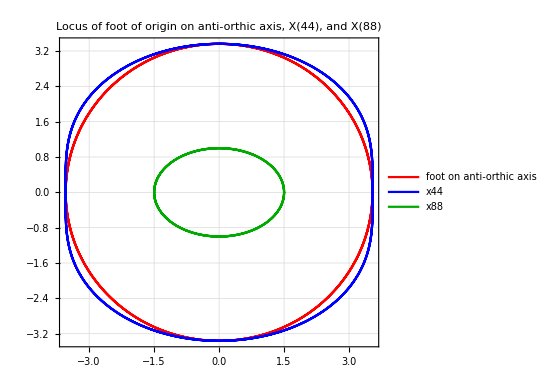

```mathematica
Module[{oaf,x44,x88,o,s,a=1.5,lab},
oaf=Quiet@ParametricPlot[getAntiorthicAxisFoot[a,{0,0},t],{t,-.0001,2π-.0001},PlotStyle->Red];
x44=Quiet@ParametricPlot[
o=orbitNormals[a,t][[1]];
s=RotateLeft@triLengths@o;
getX44Trilin[o,s],{t,0,2π},PlotStyle->Blue];
x88=Quiet@ParametricPlot[
o=orbitNormals[a,t][[1]];
s=RotateLeft@triLengths@o;
getX88Trilin[o,s],{t,0,2π},PlotStyle->Darker@Green];
lab="Locus of foot of origin on anti-orthic axis, X(44), and X(88)";
Legended[Show[{oaf,x44,x88},PlotLabel->Style[lab,{Black,Medium}],Frame->True,GridLines->Automatic],LineLegend[{Red,Blue,Darker@Green},{"foot on anti-orthic axis","x44","x88"}]]]
```

## Peter Moses' Billiard Points

```mathematica
Clear@getMosesTrilinears;
getMosesTrilinears[tri_,{a_,b_,c_}]:=Module[{ctrs,
sinA,sinB,sinC,
cosA,cosB,cosC,
cosA2,cosB2,cosC2,(*squared*)
cosA3,cosB3,cosC3,(*cubed*)
secA,secB,secC,
a2,b2,c2,a3,b3,c3,a4,b4,c4,
cirR,cir,ort,d34},
a2=a*a;b2=b*b;c2=c*c;
a3=a2*a;b3=b2*b;c3=c2*c;
a4=a2*a2;b4=b2*b2;c4=c2*c2;
cirR=getCircumradius[{a,b,c}];
cir=getCircumcenter@@tri;
ort=getOrthocenter@@tri;
d34=magn[cir-ort];
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1./{cosA,cosB,cosC};
{cosA2,cosB2,cosC2}=(#^2)&/@{cosA,cosB,cosC};
{cosA3,cosB3,cosC3}=(#^3)&/@{cosA,cosB,cosC};
ctrs={
{"X","name","trilinears"},
{190,"YFF PARABOLIC POINT",{b c/(b-c),c a/(c-a),a b/(a-b)}},
{651,"TRILINEAR POLE OF LINE X(1)X(3)",1/{(b-c)(b+c-a),(c-a)(c+a-b),(a-b)(a+b-c)}},
{653,"TRILINEAR POLE OF LINE X(1)X(4)",1/{(secB - secC),(secC - secA),(secA - secB),{}}},
{655,"TRILINEAR POLE OF LINE X(1)X(5)",1/{
cosA cosB+sinA sinB-cosC cosA-sinA sinB,
cosB cosC+sinB sinC-cosA cosB-sinB sinC,
cosC cosA+sinC sinA-cosB cosC-sinC sinA}
},
{658,"TRILINEAR POLE OF LINE X(1)X(7)",1/{
(1+cosA)(cosB-cosC),
(1+cosB)(cosC-cosA),
(1+cosC)(cosA-cosB)}
},
{660,"TRILINEAR POLE OF LINE X(1)X(39)",1/{
(a2-b c)(b-c),
(b2-c a)(c-a),
(c2-a b)(a-b)}},
{662,"TRILINEAR POLE OF LINE X(1)X(21)",1/{b2-c2,c2-a2,a2-b2}},
{673,"TRILINEAR POLE OF LINE X(1)X(514)",{
(b c)/(b2+c2-a(b+c)),
(c a)/(c2+a2-b(c+a)),
(a b)/(a2+b2-c(a+b))}
},
{771,"ISOGONAL CONJUGATE OF X(770)", 1/{cosB3-cosC3,cosC3-cosA3,cosA3-cosB3}},
{799,"ISOGONAL CONJUGATE OF X(798)",1{(1-cosA2)(cosB2-cosC2),(1-cosB2)(cosC2-cosA2),(1-cosC2)(cosA2-cosB2)}},
{823,"ISOGONAL CONJUGATE OF X(822)",{
b2 c2/((b2-c2)(b2+c2-a2)^2),
c2 a2/((c2-a2)(c2+a2-b2)^2),
a2 b2/((a2-b2)(a2+b2-c2)^2)}},
{897,"ISOGONAL CONJUGATE OF X(896)",1/{2a2-b2-c2,2 b2-c2-a2,2c2-a2-b2}},
{1156,"ISOGONAL CONJUGATE OF X(1155)",1/{
(b-c)^2 + a(b+c-2a),
(c-a)^2 + b(c+a-2b),
(a-b)^2 + c(a+b-2c)
}
},
{1492,"COLUMBUS POINT",1/{b3-c3,c3-a3,a3-b3}},
{1821,"ISOGONAL CONJUGATE OF MIMOSA TRANSFORM OF X(287)", 1/{
a2(a2 b2+a2 c2-b4-c4),
b2(b2 c2+b2 a2-c4-a4),
c2(c2 a2+c2 b2-a4-b4)}
},
{2349,"X(2)-ISOCONJUGATE OF X(1495)",1/{
(b2-c2)^2+a2(b2+c2-2a2),
(c2-a2)^2+b2(c2+a2-2b2),
(a2-b2)^2+c2(a2+b2-2c2)}
},
(* X(1113)=1st EULER-LINE-CIRCUMCIRCLE INTERSECTION
Trilinears (R-d) cosA - 2R cosB cosC,where R=circumradius,d=distance|OH|between X(3) and X(4).(Joe Goggins,2002)*)
{2580,"X(6)-ISOCONJUGATE OF X(2574)",{
((cirR-d34)cosA-2cirR cosB cosC)/a,
((cirR-d34)cosB-2cirR cosC cosA)/b,
((cirR-d34)cosC-2cirR cosA cosB)/c
}
},
(* Trilinears (1/a)f(a,b,c):(1/b)f(b,c,a):(1/c)/f(c,a,b),where f(a,b,c) is as at X(1114):
Trilinears (R+d) cosA - 2R cosB cosC *)
{2581,"X(6)-ISOCONJUGATE OF X(2575)",{
((cirR+d34)cosA-2cirR cosB cosC)/a,
((cirR+d34)cosB-2cirR cosC cosA)/b,
((cirR+d34)cosC-2cirR cosA cosB)/c}
},
{3257,"ISOGONAL CONJUGATE OF X(1635)",1/{
(b-c)(b+c-2a),
(c-a)(c+a -2b),
(a-b)(a+b -2c)}
},
(*Barycentrics: 1/[(b - c)(ab + ac - bc)]*)
{4598,"TRILINEAR POLE OF THE LINE X(1)X(87)",1/{
a(b-c)(a b+a c-b c),
b(c-a)(b c+b a-c a),
c(a-b)(c a+c b-a b)}
},
(* Barycentrics: a/(b4 - c4)*) 
{4599,"TRILINEAR POLE OF THE LINE X(1)X(82)",1/
{b4-c4,
c4-a4,
a4-b4}},
(* Barycentrics: a/[(b - c)(2b+2c-a)]*)
{4604,"TRILINEAR POLE OF THE LINE X(1)X(89)",1/{
(b-c)(2b+2c-a),
(c-a)(2c+2a-b),
(a-b)(2a+2b-c)
}},
(* Barycentrics: a/[(b - c)(3a + b + c)] *)
{4606,"TRILINEAR POLE OF THE LINE X(1)X(210)",1/{
(b-c)(3a+b+c),
(c-a)(3b+c+a),
(a-b)(3c+a+b)
}},
(* Barycentrics: 1/[(b - c)(ab + ac - 2bc)] *)
{4607,"TRILINEAR POLE OF THE LINE X(1)X(190)",1/{
a(b-c)(a b+a c-2b c),
b(c-a)(b c+b a-2c a),
c(a-b)(c a+c b-2a b)
}
},
(* Barycentrics: 1/[(b - c)(a^3 + b^3 + c^3 + abc + 2b^2 c + 2bc^2)] *)
{8052,"ISOTOMIC CONJUGATE OF X(8045)",1/{
a(b-c)(a3+b3+c3 + a b c + 2b2 c + 2b c2),
b(c-a)(b3+c3+a3 + a b c + 2c2 a + 2c a2),
c(a-b)(c3+a3+b3 + a b c + 2a2 b + 2a b2)}
},
(* Barycentrics: a/(a b^2 + a c^2 - b^2 c - b c^2) *)
{20332,"(name pending)",1/{
a b2+a c2-b2 c-b c2,
b c2+b a2-c2 a-c a2,
c a2+c b2-a2 b-a b2}
},
(* not working *)
{23707,"ISOGONAL CONJUGATE OF X(2635)", 1/{
2 secA-secB-secC,
2 secB-secC-secA,
2 secC-secA-secB}
},
(* 1/(sin(A-B)+sin(A-C)) *)
{24624,"(A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2",1/{
sinA cosB-sinB cosA+sinA cosC-sinC cosA,
sinB cosC-sinC cosB+sinB cosA-sinA cosB,
sinC cosA-sinA cosC+sinC cosB-sinB cosC
}
},
(* Barycentrics: a (a - b) (a + b - 3 c) (a - c) (a - 3 b + c) *)
{27834,"(A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71",{(a-b) (a+b-3c)(a-c)(a-3 b+c) ,
(b-c) (b+c-3a)(b-a)(b-3 c+a) ,
(c-a) (c+a-3b)(c-b)(c-3 a+b) }
},
(* Barycentrics: b c/((b^2-c^2) ((a^2-b^2-c^2)^2-b^2 c^2)) *)
{32680,"TRILINEAR PRODUCT X(2)*X(476)",{
b c/((b2-c2) ((a2-b2-c2)^2-b2 c2))/a,
c a/((c2-a2) ((b2-c2-a2)^2-c2 a2))/b,
a b/((a2-b2) ((c2-a2-b2)^2-a2 b2))/c}}
};
{#[[1]],#[[2]],trilinearToCartesian[tri,{a,b,c},#[[3]]]}&/@Select[Rest@ctrs,Length@#[[3]]==3&]];
```

#### Test it

```mathematica
Module[{o,s,mosesCtrs},
o=orbitNormals[1.5,.1][[1]];
s=RotateLeft@triLengths@o;
mosesCtrs=getMosesTrilinears[o,s];
("X("<>ToString@#<>")")&/@First/@mosesCtrs]
```

{X(190),X(651),X(655),X(658),X(660),X(662),X(673),X(771),X(799),X(823),X(897),X(1156),X(1492),X(1821),X(2349),X(2580),X(2581),X(3257),X(4598),X(4599),X(4604),X(4606),X(4607),X(8052),X(20332),X(23707),X(24624),X(27834),X(32680)}

```mathematica
Module[{o,s,mosesCtrs},
o=orbitNormals[1.5,.1][[1]];
s=RotateLeft@triLengths@o;
mosesCtrs=getMosesTrilinears[o,s];
MapIndexed[Prepend[#1,First@#2]&,mosesCtrs]]//Grid[#,Alignment->Left]&
```

1 | 190 | YFF PARABOLIC POINT | {1.38967,-0.376432}
2 | 651 | TRILINEAR POLE OF LINE X(1)X(3) | {0.129019,-0.996294}
3 | 655 | TRILINEAR POLE OF LINE X(1)X(5) | {-0.766378,-0.859629}
4 | 658 | TRILINEAR POLE OF LINE X(1)X(7) | {-0.249697,-0.986047}
5 | 660 | TRILINEAR POLE OF LINE X(1)X(39) | {0.115533,0.997029}
6 | 662 | TRILINEAR POLE OF LINE X(1)X(21) | {0.926486,-0.786448}
7 | 673 | TRILINEAR POLE OF LINE X(1)X(514) | {-1.38967,0.376432}
8 | 771 | ISOGONAL CONJUGATE OF X(770) | {1.29874,-0.500345}
9 | 799 | ISOGONAL CONJUGATE OF X(798) | {7.13486,-12.7793}
10 | 823 | ISOGONAL CONJUGATE OF X(822) | {-0.722758,-0.87626}
11 | 897 | ISOGONAL CONJUGATE OF X(896) | {-1.46377,0.218467}
12 | 1156 | ISOGONAL CONJUGATE OF X(1155) | {-1.12591,0.660748}
13 | 1492 | COLUMBUS POINT | {0.703777,-0.8831}
14 | 1821 | ISOGONAL CONJUGATE OF MIMOSA TRANSFORM OF X(287) | {-0.780268,0.854057}
15 | 2349 | X(2)-ISOCONJUGATE OF X(1495) | {0.0800296,0.998576}
16 | 2580 | X(6)-ISOCONJUGATE OF X(2574) | {-0.667218,-0.895624}
17 | 2581 | X(6)-ISOCONJUGATE OF X(2575) | {0.937082,0.780848}
18 | 3257 | ISOGONAL CONJUGATE OF X(1635) | {-0.383844,0.966704}
19 | 4598 | TRILINEAR POLE OF THE LINE X(1)X(87) | {1.49828,0.0478784}
20 | 4599 | TRILINEAR POLE OF THE LINE X(1)X(82) | {0.48072,-0.947255}
21 | 4604 | TRILINEAR POLE OF THE LINE X(1)X(89) | {0.686489,-0.889128}
22 | 4606 | TRILINEAR POLE OF THE LINE X(1)X(210) | {1.25297,-0.549769}
23 | 4607 | TRILINEAR POLE OF THE LINE X(1)X(190) | {0.643039,0.90345}
24 | 8052 | ISOTOMIC CONJUGATE OF X(8045) | {1.23517,-0.567397}
25 | 20332 | (name pending) | {-1.4573,-0.236892}
26 | 23707 | ISOGONAL CONJUGATE OF X(2635) | {0.0458986,0.999532}
27 | 24624 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2 | {-1.27381,0.52806}
28 | 27834 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71 | {1.41399,0.333757}
29 | 32680 | TRILINEAR PRODUCT X(2)*X(476) | {-1.48265,0.151654}

## Main Axis Sim

```mathematica
Clear@getIsotomicAxisLow;
getIsotomicAxisLow[tri_,sides_,actData_]:=Module[{axisPts},
(*<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];*)
axisPts=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{actData["tri"],RotateLeft@actData["tri"],actData["tps"],RotateLeft@actData["tps"]}];
axisPts];
```

#### Perp. to orthic (isogonal) axis : X(1)X(3) Perp. to isotomic axis : X(1)X(7) [gergonne point]

```mathematica
perpAntiorthicAndIsotomic[a_,t_]:=Module[{o,n,s,inc,bar,cir,exc,aoa,actData,ita,ger},
{o,n}=orbitNormals[a,t];
s=RotateLeft@triLengths@o;
inc=getIncenter[o[[1]],n[[1]],o[[2]],n[[2]]];
bar=getBaricenter@@o;
cir=getCircumcenterTrilin[o,s];
ger=getGergonneTrilin[o,s];
exc=excentralTriangle[o,s];
(* isogonal / anti-orthic *)
aoa=getAntiOrthicAxis[o,exc];
actData=getAnticomplData[o,s];
(* isotomic *)
ita=getIsotomicAxisLow[o,s,actData];
(* euler line of excentral triangle is perp to its axis, but this line goes thru X(1) and X(3) *)
{"aoaX1X3"-> (inc-cir).(aoa[[2]]-aoa[[1]]),
"itaX1X3"->(inc-cir).(ita[[2]]-ita[[1]]),(* doesn't work!*)
"itaX1X7"-> (inc-ger).(ita[[2]]-ita[[1]])(* works! *)
}]
```

```mathematica
{"aoaX1X3","itaX1X7"}/.Table[perpAntiorthicAndIsotomic[1.5,t],{t,.01,π-.01,π/10.}]
```

{{-8.88178×10^-15,6.10623×10^-15},{-1.55431×10^-15,-3.60822×10^-16},{3.55271×10^-15,-3.88578×10^-15},{3.55271×10^-15,2.33147×10^-15},{-9.76996×10^-15,8.21565×10^-15},{-1.28786×10^-13,1.42109×10^-13},{3.55271×10^-15,-6.66134×10^-15},{1.33227×10^-15,-2.55351×10^-15},{3.33067×10^-16,1.05471×10^-15},{-3.41949×10^-14,5.75096×10^-14}}

```mathematica
Clear@getIsotomicAxis;
getIsotomicAxis[tri_]:=Module[{sides,actData,x100,x693,x693trilin,
(*actTpsIsotConj*)
actTpsIsogConj,axisPts,noise},
sides=RotateLeft@triLengths@tri;
(*<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];*)
actData=getAnticomplData[tri,sides];
x100=getX100Trilin[tri,sides];
x693=isotomicConjugate[x100,tri][[1]];
x693trilin=getX693Trilin[tri,sides];
axisPts=getIsotomicAxisLow[tri,sides,actData];
actTpsIsogConj=isogonalConjugate[#,tri,getTriBisectors@@tri]&/@(actData["tps"]);
(*noise=RandomReal[{-1,1},2]*10^-6;
actTpsIsotConj=(isotomicConjugate[#+noise,tri][[1]])&/@(actData["tps"]);
*)
<|"x100"->x100,
"x693"->x693,
"x693trilin"->x693trilin,
"act"->actData["tri"],
"actTps"->actData["tps"],
"actInc"->actData["inc"],
"actIncR"->actData["incR"],
"axisPts"->axisPts,
"actTpsIsogConj"->actTpsIsogConj
(*,"actTpsIsotConj"->actTpsIsotConj*)|>];
```

```mathematica
getIsotomicAxis[{{0,0},{1.,0},{2,2}}]
```

<|x100→{2.05725,1.22621},x693→{7.66134,5.5968},x693trilin→{7.66134,5.5968},act→{{3.,2.},{1.,2.},{-1.,-2.}},actTps→{{0.817697,1.63539},{1.87403,0.874032},{1.40764,2.}},actInc→{1.40764,1.34042},actIncR→0.659577,axisPts→{{0.311835,2.},{1.22295,2.44589},{5.57649,4.57649}},actTpsIsogConj→{{2.06078,-0.686928},{-10.9078,-3.96926},{2.83069,-0.492066}}|>

```mathematica
showAntiOrthicAxis;
Options@showAntiOrthicAxis={tIsogonal->0,tIsotomic->0,drSteiner->False,drX1->False,drCircum->False,drAoaConstr->False,drItaConstr->False,drX88->False,drAoaFoot->False,drPerps->False,drDarboux->False,drDarbouxAxis->False,drAntiContact->False,drIsogonalSample->False,drIsotomicSample->False,drIsogLim->False,drIsotLim->False,drPeterMoses1k->False,drPeterMosesAbove1k->False,drPeterMosesAbove4k->False,drAxes->False,pointSize->Medium,fontSize->Medium,labelDist->.1,maxX->4,maxY->4,drNotables->True};
Clear@showAntiOrthicAxis;showAntiOrthicAxis[a_,t_,OptionsPattern[]]:=Module[{o,n,s,ell,exc,
aoa (*anti-orthic/isogonal axis*),ita,(*isotomic axis*)
aoaPerp,itaPerp,
cir,inc,bar,ger,nag,x44,x88,x100,x144,x142,x190,
actData,
incCircumEll,incCircumEllVtx,incCircumEllVtxIsog,
incHalf,incHalfCircumEll,incHalfCircumEllVtx,incHalfCircumEllVtxIsog,
barCircumEll,barCircumEllVtx,barCircumEllVtxIsog,
gr,grAoc,x44inter,x88inter,x88isog,pEll44,pEllisog,aoaFoot,pAntiorthic,pIsotomic,
pInterAxes,pInterIsog,pInterIsot,
mosesCtrs,circRad=.1},
ell=plotEll[a];
{o,n}=orbitNormals[a,t];
s=RotateLeft@triLengths@o;
inc=getIncenter[o[[1]],n[[1]],o[[2]],n[[2]]];
bar=getBaricenter@@o;
cir=getCircumcenterTrilin[o,s];
ger=getGergonneTrilin[o,s];
nag=getNagelTrilin[o,s];
exc=excentralTriangle[o,s];
(* isogonal / anti-orthic *)
aoa=getAntiOrthicAxis[o,exc];
actData=getAnticomplData[o,s];
(* isotomic *)
ita=getIsotomicAxisLow[o,s,actData];
(* euler line of excentral triangle is perp to its axis, but this line goes thru X(1) and X(3) *)
aoaPerp=interRays[inc,inc-cir,aoa[[1]],aoa[[2]]-aoa[[1]]];
itaPerp=interRays[inc,inc-ger,ita[[1]],ita[[2]]-ita[[1]]];
x144=getX144Trilin[o,s];
x44inter=interRays[{0,0},inc,First@aoa,Second@aoa-First@aoa];
x44=getX44Trilin[o,s];
x88=getX88Trilin[o,s];
x100=getX100Trilin[o,s];
x190=getX190Trilin[o,s];
x142=getX142Trilin[o,s];
x88isog=isogonalConjugate[x44,o,n];
pEll44=inc*Sqrt[magn@x44/magn@inc];
pEllisog=isogonalConjugate[pEll44,o,n];
x88inter=interRays[{0,0},x88,First@aoa,Second@aoa-First@aoa];
aoaFoot=closestPerp[{0,0},First@aoa,Second@aoa];
pAntiorthic=ray[aoaFoot,norm[x44-aoaFoot],OptionValue@tIsogonal];
pIsotomic=ray[ita[[2]],norm[ita[[3]]-ita[[2]]],OptionValue@tIsotomic];
pInterAxes=interRays[aoaFoot,x44-aoaFoot,ita[[2]],ita[[3]]-ita[[2]]];
pInterIsog=isogonalConjugate[pInterAxes,o,n];
pInterIsot=isotomicConjugate[pInterAxes,o][[1]];
incCircumEll=getCircumAny[o,inc];
incCircumEllVtx=incCircumEll["vertices"];
incCircumEllVtxIsog=isogonalConjugate[#,o,n]&/@incCircumEllVtx;
incHalf=inc/2;
incHalfCircumEll=getCircumAny[o,incHalf];
incHalfCircumEllVtx=incHalfCircumEll["vertices"];
incHalfCircumEllVtxIsog=isogonalConjugate[#,o,n]&/@incHalfCircumEllVtx;
barCircumEll=getCircumAny[o,bar];
barCircumEllVtx=barCircumEll["vertices"];
barCircumEllVtxIsog=isogonalConjugate[#,o,n]&/@barCircumEllVtx;
mosesCtrs=getMosesTrilinears[o,s];
gr=Graphics[{FaceForm@None,PointSize@OptionValue@pointSize,
{ellLabelPoints[a,o,"P",Medium,1.5*OptionValue@labelDist](*Text[#1,#2,{-1.5,-1.5}]&,{{"P_1","P_2","P_3"},o}]*)},
{EdgeForm@{Thick,Black},Polygon@o},
If[OptionValue@drAxes,{
{Blue,Point@aoa,Thick,Line[{First@aoa,Second@aoa,Third@aoa}]},
{Red,Point@ita,Thick,Line[ita]}},{}],
{Black,Point@{0,0},Text["X_9",{0,0},{0,1.5}]},
If[OptionValue@drNotables,MapThread[{#1,Point@#2,Text[Subscript["X",#3],#2,{-1.5,-1.5}]}&,
Transpose@{
{"inc" /.ptClrs,inc,1},
{"bar"/.ptClrs,bar,2},
{"cir"/.ptClrs,cir,3},
{"ger"/.ptClrs,ger,7},
{Darker@Green,nag,8}, (* he is the incenter of the anticompl triangle *)
{"tab"/.ptClrs,x142,142}, (* mittenpunkt of the medial triangle -- not shown *)
{"dar"/.ptClrs,x144,144} (* perspector of anticompl triangle with its contact triangle *)
}],{}],
{Red,PointSize@OptionValue@pointSize,
Point@x100,ellLabelTxt[a,x100,"X_100",OptionValue@labelDist,inward->False],
Point@x190,ellLabelTxt[a,x190,"X_190",OptionValue@labelDist,inward->False],
Point@x88,ellLabelTxt[a,x88,"X_88",OptionValue@labelDist,inward->False]},
If[OptionValue@drAntiContact,
{{Darker@Green,Thick,Circle[nag,actData["incR"]]},
{EdgeForm@Darker@Green,Polygon@actData["tps"],Darker@Green,Point@actData["tps"]},
{EdgeForm@Blue,Polygon@actData["tri"]}
},{}],
If[OptionValue@drDarbouxAxis,{"dar"/.ptClrs,Dashed,Thick,Line[{ger,x144}],Darker@Green,Line[{x88,x100}]},{}],
If[OptionValue@drX88,{Magenta,Point@x88,Circle[x88isog,circRad],Text["X_88",x88,{-1.5,1.5}],Line[{{0,0},x88inter}],Point@x88inter,Orange,Line[{{0,0},pEllisog}],Point@pEllisog,Text["T'",pEllisog,{-1.5,-1.5}],
{Red,Point@x44inter,Circle[x44,circRad],Text["X_44",x44,{-1.5,-1.5}],Dashed,Line[{{0,0},x44inter}]},
{Red,Point@pEll44,Text["T",pEll44,{-1.25,-1.25}]}},{}],
If[OptionValue@drAoaConstr,{Darker@Darker@Green,Dashed,MapThread[Line@{#1,#2}&,{exc,aoa}],
Black,MapThread[Line@{#1,#2}&,{o,aoa}],
{Darker@Green,MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"P_1'","P_2'","P_3'"},exc}]},
{EdgeForm@{Darker@Darker@Green},Polygon@exc}},{}],
If[OptionValue@drAoaFoot,{Blue,Point@aoaFoot,Line[{{0,0},aoaFoot}],Text["foot",aoaFoot,{-1,-1}]},{}],
If[OptionValue@drCircum,{Dashed,Red,Point@cir,Circle[cir,magn[cir-o[[1]]]]},{}],
If[OptionValue@drDarboux,{Dashed,Red,Point@x144,Text["X_144",x144,{-1,-1}],MapThread[Line[{#1,#2}]&,{actData["tri"],actData["tps"]}]},{}],
If[OptionValue@drX1,{Darker@Green,Point@incCircumEllVtx,Point@incCircumEllVtxIsog,Line@incCircumEllVtxIsog,
Line[{incCircumEllVtxIsog[[2]],ray[incCircumEllVtxIsog[[2]],incCircumEllVtxIsog[[2]]-incCircumEllVtxIsog[[1]],10]}],
Line[{incCircumEllVtxIsog[[1]],ray[incCircumEllVtxIsog[[1]],incCircumEllVtxIsog[[1]]-incCircumEllVtxIsog[[2]],10]}]},{}],
If[OptionValue@drSteiner,{Darker@Pink,Point@barCircumEllVtx,Point@barCircumEllVtxIsog,Line@barCircumEllVtxIsog,
Line[{barCircumEllVtxIsog[[2]],ray[barCircumEllVtxIsog[[2]],barCircumEllVtxIsog[[2]]-barCircumEllVtxIsog[[1]],10]}],
Line[{barCircumEllVtxIsog[[1]],ray[barCircumEllVtxIsog[[1]],barCircumEllVtxIsog[[1]]-barCircumEllVtxIsog[[2]],10]}]},{}],
If[OptionValue@drIsogonalSample,{Darker@Cyan,PointSize@Large,Point@pAntiorthic,Point@isogonalConjugate[pAntiorthic,o,n]},{}],
If[OptionValue@drIsotomicSample,{Lighter@Red,PointSize@Large,Point@pIsotomic,Point@isotomicConjugate[pIsotomic,o][[1]]},{}],
If[OptionValue@drIsotLim,{PointSize@Large,{Dashed,Line[{ita[[1]],pInterAxes}],Point@pInterAxes},Lighter@Red,Point@pInterIsot},{}],
If[OptionValue@drIsogLim,{PointSize@Large,{Dashed,Line[{aoa[[1]],pInterAxes}],Point@pInterAxes},Darker@Cyan,Point@pInterIsog},{}],

If[OptionValue@drPerps,{PointSize@Large,Dashed,Blue,Line[{cir,aoaPerp}],Point@aoaPerp,Red,Line[{ger,itaPerp}],Point@itaPerp},{}],
If[OptionValue@drItaConstr,Module[{isoAxis},
isoAxis=getIsotomicAxis[o];
{{Blue,EdgeForm@Blue,Polygon@isoAxis["act"],Point@isoAxis["act"],Dashed,MapThread[Line@{#1,#2}&,{isoAxis["act" ],isoAxis["axisPts"]}]},
{Darker@Green,EdgeForm@{Darker@Green,Dashed},Polygon@isoAxis["actTps"],Point@isoAxis["actTps"],Circle[isoAxis["actInc"],isoAxis["actIncR"]],Dashed,MapThread[Line@{#1,#2}&,{isoAxis["actTps" ],isoAxis["axisPts"]}]}}],{}],
If[OptionValue@drPeterMoses1k,Module[{pmCtrs},
pmCtrs=Select[mosesCtrs,#[[1]]<=1000&];
{Point[Third/@pmCtrs],ellLabelTxt[1.5,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist]&/@pmCtrs}],{}],
If[OptionValue@drPeterMosesAbove1k,Module[{pmCtrs},
pmCtrs=Select[mosesCtrs,(#[[1]]>1000&&#[[1]]<=4000)&];
{Red,Point[Third/@pmCtrs],ellLabelTxt[1.5,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist]&/@pmCtrs}],{}],
If[OptionValue@drPeterMosesAbove4k,Module[{pmCtrs},
pmCtrs=Select[mosesCtrs,(#[[1]]>4000)&];
{Blue,Point[Third/@pmCtrs],ellLabelTxt[1.5,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist,inward->True]&/@pmCtrs}],{}]
}];

Show[{ell,gr,
If[OptionValue@drX1,drawCircumAny[o,inc,ctrLab->"",ps->{Darker@Green}],{}],
If[OptionValue@drSteiner,drawCircumAny[o,bar,ctrLab->"",ps->{Darker@Pink}],{}]
},Frame->True,PlotLabel->(Style["Antiorthic (Isogonal) and Isotomic Axes",{Large,Black}]),GridLines->Automatic,ImageSize->Large,PlotRange->{{-OptionValue@maxX,OptionValue@maxX},{-OptionValue@maxY,OptionValue@maxY}}]];
```

```mathematica
Manipulate[showAntiOrthicAxis[1.5,toRad@t,tIsogonal->(tIsogonal0^3),tIsotomic->(tIsotomic0^3),drNotables->drNotables0,maxX->maxX0,maxY->maxY0,drX1->drX10,drSteiner->drSteiner0,drCircum->drCircum0,drAoaConstr->drAoaConstr0,drItaConstr->drItaConstr0,drX88->drX880,drDarboux->drDarboux0,drAntiContact->drAntiContact0,drDarbouxAxis->drDarbouxAxis0,drAoaFoot->drAoaFoot0,drPerps->drPerps0,
drIsogonalSample->drIsog0,drIsotomicSample->drIsot0,drIsogLim->drIsogLim0,drIsotLim->drIsotLim0,
drPeterMoses1k->drPeterMoses1k0,drPeterMosesAbove1k->drPeterMosesAbove1k0,drPeterMosesAbove4k->drPeterMosesAbove4k0,drAxes->drAxes0],
{{t,25},-360,360,1,Appearance->"Labeled"},
{{tIsotomic0,1,"isotomic t"},-10,10,.01,Appearance->"Labeled"},
{{tIsogonal0,1,"isogonal t"},-10,10,.01,Appearance->"Labeled"},
{{maxX0,4},{2,4,6,8,20,30}},
{{maxY0,4},{2,4,6,8,20,30}},
{{drNotables0,False,"notables"},{True,False}},
{{drAxes0,True,"Isog+Isot Axes"},{True,False}},
{{drX10,False,"Incenter circumell."},{True,False}},
{{drSteiner0,False,"Steiner (X_1) circumell."},{True,False}},
{{drCircum0,False,"circumcircle"},{True,False}},
{{drAoaConstr0,False,"isogonal axis construction"},{True,False}},
{{drItaConstr0,False,"isotomic axis construction"},{True,False}},
{{drX880,False,"X_88 and X_44"},{True,False}},
{{drDarboux0,False,"Darboux Point = X_144"},{True,False}},
{{drDarbouxAxis0,False,"Darboux Axis"},{True,False}},
{{drAntiContact0,False,"Anticompl. Contact"},{True,False}},
{{drPerps0,False,"axis perpendiculars"},{True,False}},
{{drAoaFoot0,False,"antiorthic foot"},{True,False}},

{{drIsot0,True,"isotomic sample"},{True,False}},
{{drIsog0,True,"isogonal sample"},{True,False}},
{{drIsotLim0,False,"isotomic inter"},{True,False}},
{{drIsogLim0,False,"isogonal inter"},{True,False}},

{{drPeterMoses1k0,False,"Moses-X_9 (to X_(1  k))"},{True,False}},
{{drPeterMosesAbove1k0,False,"Moses-X_9 (above X_(1  k))"},{True,False}},
{{drPeterMosesAbove4k0,False,"Moses-X_9 (above X_(4  k))"},{True,False}}
,ControlPlacement->Left]
```

```mathematica
(*DeleteFile[CloudDeploy[%,"antiorthic and isotomic axes",Permissions->"Public"]]*)
```

```mathematica
(*CloudDeploy[%,"antiorthic and isotomic axes",Permissions->"Public"]*)
```

```mathematica
Clear@showOneMosesFrame;showOneMosesFrame[a_,tDeg_,showAntiContact_:True]:=Show[showAntiOrthicAxis[a,toRad@tDeg+.001,0,0,maxX->2 ,maxY->1.5,
drDarbouxAxis->showAntiContact,
drAntiContact->showAntiContact,
drPeterMoses1k->True,
drPeterMosesAbove1k->True,
pointSize->Large,labelDist->0.075,
drPeterMosesAbove4k->True],PlotLabel->Style["Points on X_9-Centered Circumellipse\na="<>nfn[a,2]<>",θ="<>nfn[tDeg,1],{Black,Large}],ImageSize->800]
```

```mathematica
Manipulate[
showOneMosesFrame[1.5,tDeg,antiContact],
{{tDeg,30},-360,360,1},
{{antiContact,False,"Anticompl. Contact"},{True,False}}]
```

```mathematica
(*DeleteFile[mosesDeploy]*)
```

```mathematica
mosesDeploy=CloudDeploy[%,"peter moses points on X9-centered circumellipse",Permissions->"Public"]
```

CloudObject[]

## Movie Utils

```mathematica
Clear@doMovieFrames;
Options@doMovieFrames=Join[Options@movieFrame,{step->toRad@1.,offset->.0001}];
doMovieFrames[a_,exp_,lociFn_,view_:"excHalf",opts:OptionsPattern[]]:=Module[{loci,ellPlot,causticPlot,excenterLims,showables},
ellPlot=plotEllFill[1.5,Directive[Blue,Opacity@.1],{Thick,Black}];
causticPlot=plotEllb[Sequence@@getTriCausticParams[a],"feu"/.ptClrs];
(*loci=precompLoci[a];*)
loci=Quiet[lociFn[a]];
excenterLims=excenterMax[a];
showables=Join[getExpShowables[exp],{"loci","orbit"}];
(*Print["a=",a,",t=",0,",ellPlot=",ellPlot,",loci=",loci,",excL=",excenterLims,",view=",view,",opts=",FilterRules[{opts,showablesOpt->showables},Options@movieFrame]];*)
Table[movieFrame[a,t,ellPlot,causticPlot,loci,excenterLims,view,FilterRules[{opts,showablesOpt->showables},Options@movieFrame]],{t,OptionValue@offset,2.π+OptionValue@offset,OptionValue@step}]];
```

```mathematica
Clear@makeMovie;
makeMovie[fname_,frames_,repeats_:3]:=Module[{framesConcat},
framesConcat=Flatten@ConstantArray[frames,repeats];
Print["Exporting "<>ToString@Length[framesConcat]<>" frames to "<>fname];
Export[fname,framesConcat,"VideoEncoding"->"MPEG-4 Video"];
];
```

## Make Movies

```mathematica
imgMoses=False;
If[imgMoses,Module[{imgs},
imgs=Table[showOneMosesFrame[1.5,tDeg],{tDeg,0,360,.25}];
makeMovie["moses v2.mov",imgs,2]]];
```

```mathematica
imgMosesDarboux=False;
If[imgMosesDarboux,Module[{imgs},
imgs=Table[showOneMosesFrame[1.5,tDeg],{tDeg,0,360,.125}];
makeMovie["moses v4.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 11524 frames to moses v4.mov

## Isotomic Axis (should contain X(693) =X’(100), e os conj. isot dos pes dos incirculo do ACT)

#### Also: X (100) = trilinear pole of line X(1)X (6) (and PU (28)) (van Aubel line of excentral triangle)

```mathematica
(*CloudDeploy[%,"isotomic axis",Permissions->"Public"]*)
```

```mathematica
Clear@drawIsotomicAxis;
drawIsotomicAxis[tri_,sides_,actData_,clr_:Darker@Cyan]:=Module[{isoAxis},
isoAxis=getIsotomicAxisLow[tri,sides,actData];
Graphics@{PointSize@Large,clr,PointSize@Large,Point@isoAxis,Thick,Line[Part[isoAxis,{1,2,3}]]}];
```

```mathematica
Clear@showIsotomicAxis;
showIsotomicAxis[a_,t_,maxX_:20,maxY_:20]:=DynamicModule[{tri,bis,sides,ell,isoAxis,tpsIsogC,gr,lgt=.2,tsamples,ellSamples,ellSamplesIsotomConj,triIsog,ellSamplesIsogonConj,x44,exc,aoa,lab,ellSampleNum=100},
ell=plotEll[a];
{tri,bis}=orbitNormals[a,t];
sides=RotateLeft@triLengths@tri;
isoAxis=getIsotomicAxis[tri];
tpsIsogC=isoAxis["actTpsIsogConj"];
ellSamples={a Cos@#,Sin@#}&/@RandomReal[{0.001,2π-.001},ellSampleNum];
(* external calc of C2 works but here it doesn't, had to add noise *)
(*xxx={-0.00302662,-0.9999979};
Print["tps2=",isoAxis["actTps"][[2]],",isotC2xxx=",isotomicConjugate[xxx,tri]];*)
ellSamplesIsotomConj=isotomicConjugate[#,tri][[1]]&/@ellSamples;
ellSamplesIsogonConj=isogonalConjugate[#,tri,bis]&/@ellSamples;
x44=getX44Trilin[tri,sides];
exc=excentralTriangle[tri,sides];
(* X(513) = isog conj do X(100), lies on line at infinity *)
(*fbarIsogC=isogonalConjugate[isoAxis["x100"]+RandomReal[{-1,1},2]*10^-6,tri,bis];*)
gr=Graphics[{FaceForm@None,PointSize@Large,Thick,
{Black,EdgeForm@Black,Polygon@tri,Point@tri,ellLabelPoints[a,tri,"P",16,lgt]},
{Blue,EdgeForm@Blue,Polygon@isoAxis["act"],Point@isoAxis["act"]},
{Darker@Green,EdgeForm@{Darker@Green,Dashed},Polygon@isoAxis["actTps"],Point@isoAxis["actTps"],ellLabelPoints[a,isoAxis["actTps"],"C",16,lgt],Circle[isoAxis["actInc"],isoAxis["actIncR"]]},
{Red,Point@isoAxis["x100"],ellLabelTxt[a,isoAxis["x100"],Style[OverBar["F"],16],lgt]},
{Orange,Point@tpsIsogC,labelPoints[tpsIsogC,"C''",14,{1,-1.5}],Dashed,Line[{tpsIsogC[[1]],tpsIsogC[[3]]}]},
{Red,Point@isoAxis["x693"],Text[Style["X_693",16],isoAxis["x693"],{-1.5,-1.5}]},
{PointSize@Small,Darker@Cyan,Point@ellSamplesIsotomConj},
{PointSize@Small,Darker@Cyan,PointSize@Large,Point@isoAxis["axisPts"],Thick,Line[Part[isoAxis["axisPts"],{1,2,3}]]},
{PointSize@Small,Orange,Point@ellSamplesIsogonConj},
{PointSize@Large,Orange,Point@x44,Text[Style["X_44",16],x44,{1,-1.5}]}
(*,{PointSize@Large,Orange,Point@fbarIsogC,Text[Style[OverBar["F"],16],fbarIsogC,{-1.5,-1.5}]}*)
(*{EdgeForm@{Darker@Green,Dashed},Polygon@exc}*)}];
lab=(Style["Isotomic and Isogonal Points",{Large,Black}]);
Show[{ell,drawAntiOrthicAxis[tri,exc,False],gr},Frame->True,PlotLabel->lab,GridLines->Automatic,ImageSize->Large,PlotRange->{{-maxX,maxX},{-maxY,maxY}}]];
```

```mathematica
isotomicConjugate[{-.00302663,-.999998},{{1.49,-.087},{-1.34,-.45},{-.79,.85}}][[1]]
```

{2.54552,-2.04522}

```mathematica
Manipulate[showIsotomicAxis[1.5,toRad[t+.0001],maxX,maxY],
{{t,-5},-360,360,1,Appearance->"Labeled"},
{{maxX,8},{2,4,8,12,24}},{{maxY,8},{2,4,8,12,24}},ControlPlacement->Left]
```